## Init

```mathematica
Clear[AnalysePoints]
AnalysePoints[pts_]:=Module[{analysed},
analysed["vals"]={Union[N[pts[[All,1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[N[pts[[All,2]]],SameTest->(Abs[#1-#2]≤0.001&)],Union[N[pts[[All,3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
analysed["diffs"]={
Union[Rest[analysed["vals"][[1]]]-Most[analysed["vals"][[1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[2]]]-Most[analysed["vals"][[2]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[3]]]-Most[analysed["vals"][[3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
 analysed
]
```

```mathematica
Clear[AnalyseTransform,indx,shift,dim,analysed,bins,indxBins,diffvec,ErrorVecs];
AnalyseTransform[ T_,S_,c_,n_,fun_:Round]:=Module[{indx,dim,analysed,bins,indxBins,diffvec,ErrorVecs},
analysed["pts"]=Table[N[S(T.{r,g,b})+c],{r,0,n},{g,0,n},{b,0,n}];
analysed["orderedPts"]= Sort[Flatten[analysed["pts"],2]];
analysed["range"]={
{Min[analysed["pts"][[All,All,All,1]]],Max[analysed["pts"][[All,All,All,1]]]},{Min[analysed["pts"][[All,All,All,2]]],Max[analysed["pts"][[All,All,All,2]]]},{Min[analysed["pts"][[All,All,All,3]]],Max[analysed["pts"][[All,All,All,3]]]}};
analysed["vals"]={Union[N[analysed["pts"][[All,1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[N[analysed["pts"][[All,2]]],SameTest->(Abs[#1-#2]≤0.001&)],Union[N[analysed["pts"][[All,3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
analysed["diffs"]={
Union[Rest[analysed["vals"][[1]]]-Most[analysed["vals"][[1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[2]]]-Most[analysed["vals"][[2]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[3]]]-Most[analysed["vals"][[3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
indx=fun[analysed["pts"]];
shift={1-Min[Flatten[indx[[All,All,All,1]]]],1-Min[Flatten[indx[[All,All,All,2]]]],1-Min[Flatten[indx[[All,All,All,3]]]]};
dim={
Ceiling@Max[analysed["pts"][[All,All,All,1]]]+shift[[1]],
Ceiling@Max[analysed["pts"][[All,All,All,2]]]+shift[[2]],
Ceiling@Max[analysed["pts"][[All,All,All,3]]]+shift[[3]]};
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
indxBins=Table[{},{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Do[
Part[bins,indx[[r,g,b,1]]+shift[[1]],indx[[r,g,b,2]]+shift[[2]],indx[[r,g,b,3]]+shift[[3]]]++;
AppendTo[ Part[indxBins,indx[[r,g,b,1]]+shift[[1]],indx[[r,g,b,2]]+shift[[2]],indx[[r,g,b,3]]+shift[[3]]],analysed["pts"][[r,g,b]]];
,{r,1,n+1},{g,1,n+1},{b,1,n+1}];
diffvec[{a_List,b_List}]:=(a-b);
     errIndx=Map[diffvec,Extract[indxBins,Position[bins,num_/;num==2]]];
analysed["errIndx"]=errIndx;
ErrorVecs=Union[errIndx,SameTest->(Floor[1000000 #1]==Floor[1000000 #2]&)];
analysed["binMax"]=Max[bins];
analysed["errorVecs"]=ErrorVecs;
analysed["binCounts"]=Table[Count[LCaCbZero["bins"],num_/;num==i,3],{i,0,analysed["binMax"]}];
analysed["indx"]=indx;
analysed["bins"]=bins;
analysed
]
```

```mathematica
AnalysedTransformPrint[ analysed_]:=Module[{},
Print["Dimensions[pts] = ",Dimensions[analysed["pts"]]];
Print["Dimensions[orderedPts] = ",Dimensions[analysed["orderedPts"]]];
Print["Range = ",MatrixForm[analysed["range"]]];
Print["Max[bins]=",analysed["binMax"]];
Print[Column[{"Errors occur in directions ",Map[MatrixForm,analysed["errorVecs"]]}]];
Print[Row[{"Information loss :" ,100(1-N[Count[analysed["bins"],n_/;n>0,4]/16^3]),"%"}]]
]
```

```mathematica
SpecklePlots[bins_,l_,axis_String]:=Module[{imgSize},
imgSize=200;
Switch[axis,
"L",
GraphicsRow[
{MatrixPlot[ bins[[l-1,All,All]],ImageSize->imgSize,Mesh->All,ColorRules->{0->White,1->Red},FrameLabel->{{"Ca",Row[{"L = ",l-1}] },{"Cb",None}}],MatrixPlot[bins[[l,All,All]],ImageSize->imgSize,Mesh->All,ColorRules->{0->White,1->Green},FrameLabel->{{"Ca",Row[{"L = ",l}] },{"Cb",None}}],MatrixPlot[bins[[l+1,All,All]],ImageSize->imgSize,Mesh->All,ColorRules->{0->White,1->Blue},FrameLabel->{{"Ca",Row[{"L = ",l+1}] },{"Cb",None}}],MatrixPlot[bins[[l-1,All,All]]+2 bins[[l,All,All]]+4 bins[[l+1,All,All]],ImageSize->imgSize,Mesh->All,ColorRules->{0->Black,1->RGBColor[1,0,0],2-> RGBColor[0,1,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,1],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]},FrameLabel->{{"Cb",None},{"L",None}}] }],
"Ca",
GraphicsRow[
{MatrixPlot[ bins[[All,l-1,All]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Ca = ",l-1}] },{"Cb",None}}],
MatrixPlot[bins[[All,l,All]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Ca = ",l}] },{"Cb",None}}],
MatrixPlot[bins[[All,l+1,All]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Ca = ",l+1}] },{"Cb",None}}],MatrixPlot[bins[[All,l-1,All]]+2 bins[[All,l,All]]+4 bins[[All,l+1,All]],ImageSize->imgSize,Mesh->All,ColorRules->{0->Black,1->RGBColor[1,0,0],2-> RGBColor[0,1,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,1],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}]}
],
"Cb",
GraphicsRow[{
MatrixPlot[ bins[[All,All,l-1]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Cb = ",l-1}] },{"Ca",None}}],
MatrixPlot[bins[[All,All,l]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Cb = ",l}] },{"Ca",None}}],
MatrixPlot[bins[[All,All,l+1]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Cb = ",l+1}] },{"Ca",None}}],MatrixPlot[bins[[All,All,l-1]]+2 bins[[All,All,l]]+4 bins[[All,All,l+1]],ImageSize->imgSize,Mesh->All,ColorRules->{0->Black,1->RGBColor[1,0,0],2-> RGBColor[0,1,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,1],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}]}
]
]]
```

```mathematica
SpecklePlot[bins_,l_,axis_String]:=Module[{imgSize},
imgSize=200;
Switch[axis,
"L",
MatrixPlot[bins[[l,All,All]],ImageSize->imgSize,Mesh->All,,FrameLabel->{{"Cb",Row[{"L = ",l}] },{"Ca",None}}],
"Ca",
MatrixPlot[bins[[All,l,All]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"Cb",Row[{"Ca = ",l}] },{"L",None}}],
"Cb",
MatrixPlot[bins[[All,All,l]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"Ca",Row[{"Cb = ",l}] },{"L",None}}]
]]
```

```mathematica
SpecklePlot[bins_,l_,axis_String]:=Module[{imgSize},
imgSize=200;
Switch[axis,
"L",
MatrixPlot[Transpose[bins[[l,All,All]]],ImageSize->imgSize,Mesh->All,,FrameLabel->{{"Ca",Row[{"L = ",l}] },{"Cb",None}}],
"Ca",
MatrixPlot[Transpose[bins[[All,l,All]]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Ca = ",l}] },{"Cb",None}}],
"Cb",
MatrixPlot[Transpose[bins[[All,All,l]]],ImageSize->imgSize,Mesh->All,FrameLabel->{{"L",Row[{"Cb = ",l}] },{"Ca",None}}]
]]
```

```mathematica
Clear[ListPlot3Dto2DSlice]
ListPlot3Dto2DSlice[an_,L_,Ca_,Cb_]:=Module[{pts,rng,indx},
pts=an["pts"];
rng=an["range"];
indx= an["indx"];
Row[{
ListPlot3Dto2DSlice[pts,rng,indx,L,Ca,Cb,"Ca"],
ListPlot3Dto2DSlice[pts,rng,indx,L,Ca,Cb,"L"],
ListPlot3Dto2DSlice[pts,rng,indx,L,Ca,Cb,"Cb"]
}]
]
ListPlot3Dto2DSlice[an_,L_,Ca_,Cb_,"Ca"]:=Module[{pts,rng,indx},
ListPlot3Dto2DSlice[an["pts"],an["range"],an["indx"],L,Ca,Cb,"Ca"]
]
ListPlot3Dto2DSlice[pts_,rng_,indx_,L_,Ca_,Cb_,"Ca",pm:{_,_}:{0,3},style_:{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]:=Module[{},
Show[
Table[ListPlot[Extract[pts,Position[indx,{_,indx[[L,Ca+i-1+pm[[1]],Cb,2]],_}]][[All,{1,3}]],PlotStyle->style[[i]]],
{i,1,1+pm[[2]]-pm[[1]]}]
,PlotRange->{rng[[1]],rng[[3]]},Frame->True,FrameLabel->{{"Cb",None},{"L",None}},GridLines->{Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[1,1]]],Ceiling[rng[[1,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[1,1]]]+0.5,Ceiling[rng[[1,2]]]+0.5]]},1],Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[3,1]]],Ceiling[rng[[3,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[3,1]]]+0.5,Ceiling[rng[[3,2]]]+0.5]]},1]},ImageSize->300,AspectRatio->1]
]

ListPlot3Dto2DSlice[an_,L_,Ca_,Cb_,"L"]:=Module[{},
ListPlot3Dto2DSlice[an["pts"],an["range"],an["indx"],L,Ca,Cb,"L"]
]

ListPlot3Dto2DSlice[pts_,rng_,indx_,L_,Ca_,Cb_,"L",pm:{_,_}:{0,3},style_:{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]:=Module[{},
Show[
Table[ListPlot[Extract[pts,Position[indx,{indx[[L+i-1+pm[[1]],Ca,Cb,1]],_,_}]][[All,{2,3}]],PlotStyle->style[[i]]],
{i,1,1+pm[[2]]-pm[[1]]}]
,PlotRange->{rng[[2]],rng[[3]]},Frame->True,FrameLabel->{{"Cb",None},{"Ca",None}},GridLines->{Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[2,1]]],Ceiling[rng[[2,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[2,1]]]+0.5,Ceiling[rng[[2,2]]]+0.5]]},1],Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[3,1]]],Ceiling[rng[[3,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[3,1]]]+0.5,Ceiling[rng[[3,2]]]+0.5]]},1]},ImageSize->300,AspectRatio->1]
]



ListPlot3Dto2DSlice[an_,L_,Ca_,Cb_,"Cb"]:=Module[{},
ListPlot3Dto2DSlice[an["pts"],an["range"],an["indx"],L,Ca,Cb,"Cb"]
]

ListPlot3Dto2DSlice[pts_,rng_,indx_,L_,Ca_,Cb_,"Cb",pm:{_,_}:{0,3},style_:{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]:=Module[{},
Show[
Table[ListPlot[Extract[pts,Position[indx,{_,_,indx[[L,Ca,Cb+i-1+pm[[1]],3]]}]][[All,{1,2}]],PlotStyle->style[[i]]],
{i,1,1+pm[[2]]-pm[[1]]}]
,PlotRange->{rng[[1]],rng[[2]]},Frame->True,FrameLabel->{{"Cb",None},{"L",None}},GridLines->{Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[1,1]]],Ceiling[rng[[1,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[1,1]]]+0.5,Ceiling[rng[[1,2]]]+0.5]]},1],Flatten[{Map[{#,Dashed}&,Range[Floor[rng[[2,1]]],Ceiling[rng[[2,2]]]]],Map[{#,Thick}&,Range[Floor[rng[[2,1]]]+0.5,Ceiling[rng[[2,2]]]+0.5]]},1]},ImageSize->300,AspectRatio->1]
]
```

```mathematica
Flatten[{Map[{#,Dashed}&,Range[Floor[0],Ceiling[10]]],Map[{#,Thick}&,Range[Floor[0]+0.5,Ceiling[10]+0.5]]},1]
```

{{0,Dashing[{Small,Small}]},{1,Dashing[{Small,Small}]},{2,Dashing[{Small,Small}]},{3,Dashing[{Small,Small}]},{4,Dashing[{Small,Small}]},{5,Dashing[{Small,Small}]},{6,Dashing[{Small,Small}]},{7,Dashing[{Small,Small}]},{8,Dashing[{Small,Small}]},{9,Dashing[{Small,Small}]},{10,Dashing[{Small,Small}]},{0.5,Thickness[Large]},{1.5,Thickness[Large]},{2.5,Thickness[Large]},{3.5,Thickness[Large]},{4.5,Thickness[Large]},{5.5,Thickness[Large]},{6.5,Thickness[Large]},{7.5,Thickness[Large]},{8.5,Thickness[Large]},{9.5,Thickness[Large]},{10.5,Thickness[Large]}}

## Natural Scale Transform θ = 0

```mathematica
LCaCbZero=AnalyseTransform[ fRs[0],scale["LCaCb","nLCaCb"][0] scale["nLCaCb","fRs"][0],{0,0,0},15,Round];
AnalysedTransformPrint[ LCaCbZero]
```

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0. | 25.9808
-12.2474 | 12.2474
-10.6066 | 10.6066)

Max[bins]=2

Errors occur in directions 
{(-0.57735
-0.816497
0.),(-0.57735
0.408248
-0.707107),(-0.57735
0.408248
0.707107)}

Information loss :20.752%

```mathematica
Clear[LCaCbZeroR]
LCaCbZeroRS=Ceiling[N[15 scale["LCaCb","nLCaCb"][0]]]/15 scale["nLCaCb","fRs"][0];
LCaCbZeroR=AnalyseTransform[ fRs[0],LCaCbZeroRS,{0,0,0},15];
```

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0. | 26.
-12.5 | 12.5
-11. | 11.)

Max[bins]=2

```mathematica
scale["nLCaCb","fRs"][0]
```

{1/3,1/2,1/2}

```mathematica
Clear[LCaCbZeroR]
LCaCbZeroRS={3,2,2}  scale["nLCaCb","fRs"][0];
LCaCbZeroR=AnalyseTransform[ fRs[0],LCaCbZeroRS,{0,0,0},15];
```

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0. | 45.
-15. | 15.
-15. | 15.)

Max[bins]=1

```mathematica
LCaCbZero["errorVecs"]
```

{{-0.57735,-0.816497,0.},{-0.57735,0.408248,-0.707107},{-0.57735,0.408248,0.707107}}

```mathematica
Dimensions[LCaCbZeroR["bins"][[All,12,All]]]
```

{47,32}

```mathematica
MatrixForm[LCaCbZero["bins"][[All,12,All]]]
```

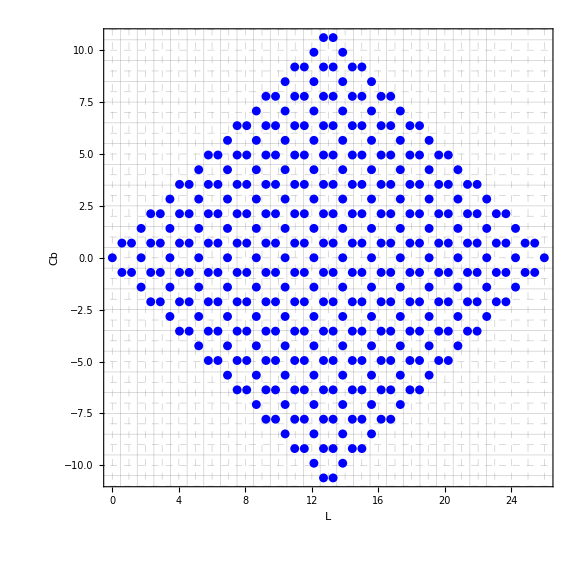

```mathematica
ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],12,12,12,"Ca",{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]
```

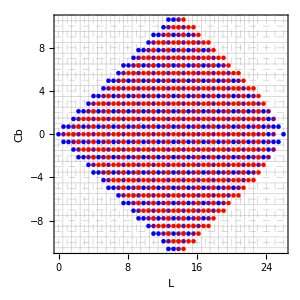
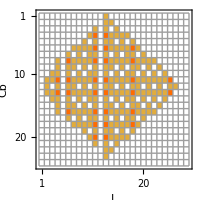

```mathematica
Row[{ListPlot3Dto2DSlice[LCaCbZero,12,12,12,"Ca"],
SpecklePlot[LCaCbZero["bins"],12,"Ca"]}]
```

```mathematica
SpecklePlot[LCaCbZero["bins"],12,"Ca"]
Head[%]
```

-Graphics-

Graphics

```mathematica
Graphics[Translate[SpecklePlot[LCaCbZero["bins"],12,"Ca"],{-0.5,-11.5}]]
```

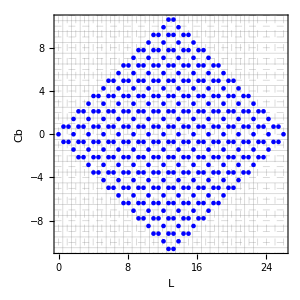
Show[{-Graphics-,-Graphics-,{-0.5,-11.5}}]

```mathematica
Show[{ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],12,12,12,"Ca",{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}],
SpecklePlot[LCaCbZero["bins"],12,"Ca"],{-0.5,-11.5}}]
```

```mathematica
Switch[bin[[i,j]],0,None,1,Red,2,Orange]
```

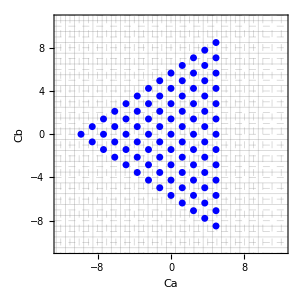

```mathematica
ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],12,12,12,"L",{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]
```

```mathematica
binPlot[bin_,xMin_,yMin_]:=Flatten[Table[{Black,EdgeForm[Thin],Switch[bin[[i,j]],0,White,1,Red,2,Orange],Rectangle[{i-1-0.5+xMin,j-0.5+yMin},{i-1+0.5,j+0.5}]},{i,1,Dimensions[bin][[1]]},{j,1,Dimensions[bin][[2]]}]];
```

```mathematica
LMin
```

{0.,25.9808}

```mathematica
CbMin
```

-10.6066

```mathematica
ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],12,12,12,"Ca",{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]
```

-Graphics-

```mathematica
Switch[axis,
"L",
,
"Ca",
,
"Cb",

]
```

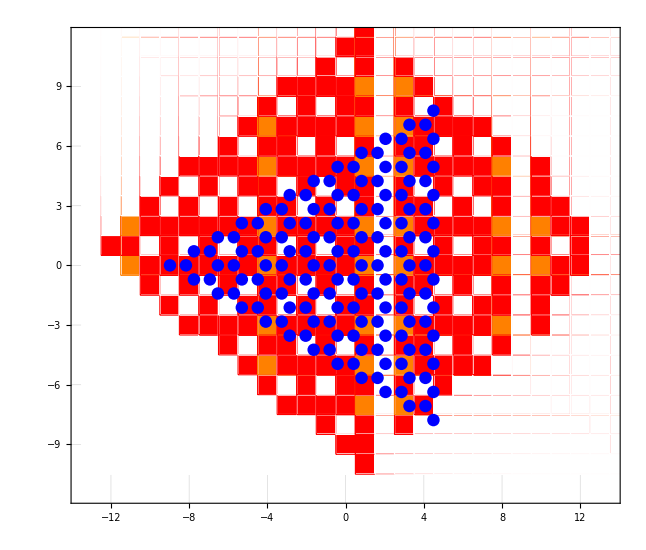

```mathematica
Block[{L=12,Ca=13,Cb=12,axis="L"},
Switch[axis,
"L",
bin=LCaCbZero["bins"][[L+1,All,All]];
axisA=2;axisB=3;s=0,
"Ca",
bin=LCaCbZero["bins"][[All,Ca+1,All]];
axisA=1;axisB=3;s=-1,
"Cb",
bin=LCaCbZero["bins"][[All,All,Cb]];
axisA=1;axisB=2;s=1;
];
bin=LCaCbZero["bins"][[All,Ca+1,All]];
aMin=Floor[LCaCbZero["range"][[axisA,1]]];
aMax=Ceiling[LCaCbZero["range"][[axisA,2]]];
bMin=Floor[LCaCbZero["range"][[axisB,1]]];
bMax=Ceiling[LCaCbZero["range"][[axisB,2]]];

Show[{Graphics[binPlot[bin,aMin,bMin+s]],
ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],L,Ca,Cb,axis,{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]},Frame->True,GridLines->Automatic,PlotRange->{{aMin-0.5,aMax+0.5},{bMin-0.5,bMax+0.5}}]
]
```

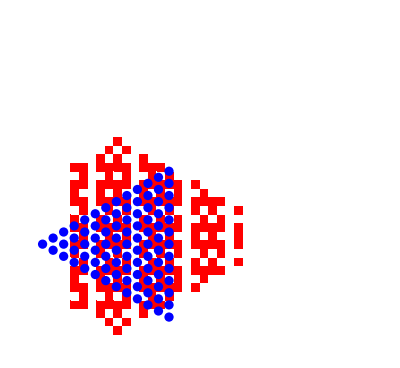

```mathematica
bin=LCaCbZero["bins"][[12,All,All]];
CaMin=-11;CbMin=-11;

Show[{Graphics[Flatten[Table[{Switch[bin[[i,j]],0,White,1,Red,2,Orange],Rectangle[{i-0.5+CaMin,j-0.5+CbMin},{i+0.5,j+0.5}]},{i,1,Dimensions[bin][[1]]},{j,1,Dimensions[bin][[2]]}]]],ListPlot3Dto2DSlice[LCaCbZero["pts"],LCaCbZero["range"],LCaCbZero["indx"],12,12,12,"L",{0,0},{Blue,Purple,Orange,Directive[Red,PointSize[Small]]}]}]
```

```mathematica
Trans
```

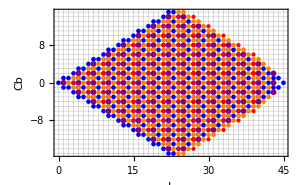
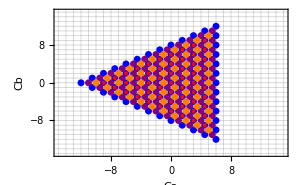
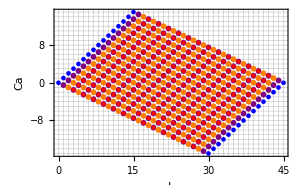

```mathematica
ListPlot3Dto2DSlice[LCaCbZeroR,12,12,12]
```

```mathematica
Manipulate[dimMax=Switch[axis,
"L",  Dimensions[LCaCbZeroR["bins"]][[1]],
"Ca",Dimensions[LCaCbZeroR["bins"]][[2]],
"Cb",Dimensions[LCaCbZeroR["bins"]][[3]]
];SpecklePlots[LCaCbZeroR["bins"],l,axis],{l,2,dimMax-1,1},{{axis,"L"},{"L","Ca","Cb"}}]
```

```mathematica
indxBins[[14,12,11]]
```

```mathematica
(Plus[#1,Times[-1,#2]])&@@{{0.5773502691896258,-0.408248290463863,-0.7071067811865475},{1.1547005383792517,0.408248290463863,-0.7071067811865475}}
```

{-0.57735,-0.816497,0.}

```mathematica
diffvec[{a_List,b_List}]:=(a-b);
errIndx=Map[diffvec,Extract[indxBins,Position[LCaCbZero["bins"],n_/;n==2]]];
ErrorVecs=Union[errIndx,SameTest->(Floor[1000000 #1]==Floor[1000000 #2]&)];
```

```mathematica
errIndx
```

{{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,-0.84375,0.},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875},{-0.583333,-0.84375,0.},{-0.583333,0.421875,-0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,0.71875},{-0.583333,0.421875,-0.71875}}

```mathematica
N[√2/2]
```

0.707107

```mathematica
fixShift = {0,√(2/3)-1,1/√2 -1}
```

{0,-1+√(2/3),-1+1/(√2)}

```mathematica
fixScale={√3, √(3/2),√2}
LCaCbZeroFixed=AnalyseTransform[ fRs[0], scale["LCaCb","nLCaCb"][0] scale["nLCaCb","fRs"][0],fixShift,15,Floor]
```

{√3,√(3/2),√2}

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0. | 25.9808
-12.431 | 12.0639
-10.8995 | 10.3137)

Max[bins]=2

analysed$114989

```mathematica
fixScale scale["LCaCb","nLCaCb"][0] scale["nLCaCb","fRs"][0]
```

{1,1,1}

```mathematica
Dimensions[LCaCbZeroFixed["bins"]]
```

{62,32,32}

```mathematica
Position[LCaCbZeroFixed["bins"],1]
```

{{16,16,16},{17,16,15},{17,16,17},{17,17,16},{18,15,14},{18,15,16},{18,15,18},{18,16,15},{18,16,17},{18,18,16},{19,14,13},{19,14,15},{19,14,17},{19,14,19},{19,16,14},{19,16,16},{19,16,18},{19,18,15},{19,18,17},{19,19,16},{20,14,12},{20,14,14},{20,14,16},4050,{57,18,16},{57,18,18},{57,18,20},{58,13,16},{58,14,15},{58,14,17},{58,16,14},{58,16,16},{58,16,18},{58,18,13},{58,18,15},{58,18,17},{58,18,19},{59,14,16},{59,16,15},{59,16,17},{59,17,14},{59,17,16},{59,17,18},{60,15,16},{60,16,15},{60,16,17},{61,16,16}}
 |  |  |  |

```mathematica
(Manipulate[GraphicsGrid[{
{MatrixPlot[ LCaCbZeroFixed["bins"][[All,All,Cb-1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[LCaCbZeroFixed["bins"][[All,All,Cb]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[LCaCbZeroFixed["bins"][[All,All,Cb+1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[LCaCbZeroFixed["bins"][[All,All,Cb-1]]+2 LCaCbZeroFixed["bins"][[All,All,Cb]]+4 LCaCbZeroFixed["bins"][[All,All,Cb+1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}],{{Cb,2},2,Dimensions[LCaCbZeroFixed["bins"]][[3]],1}])
```

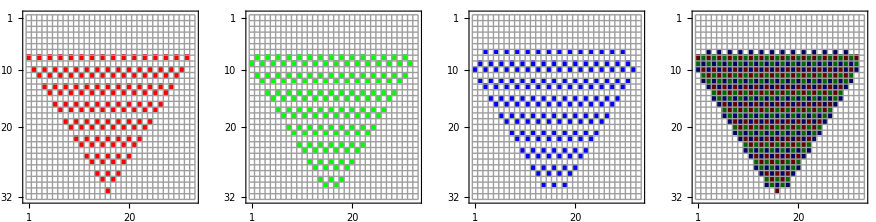

```mathematica
Block[{l=32},GraphicsGrid[{
{MatrixPlot[ (LCaCbZeroFixed["bins"])[[l-1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[LCaCbZeroFixed["bins"][[l,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[LCaCbZeroFixed["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[LCaCbZeroFixed["bins"][[l-1,All,All]]+2 LCaCbZeroFixed["bins"][[l,All,All]]+4 LCaCbZeroFixed["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}]
]
```

```mathematica
LCaCbZeroOne=AnalyseTransform[ fRs[0],{1,1,1},15]
```

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0. | 45.
-15. | 15.
-15. | 15.)

Max[bins]=1

analysed$84968

```mathematica
Block[{l=32},GraphicsGrid[{
{MatrixPlot[ (LCaCbZeroFixed["bins"])[[l-1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[LCaCbZeroFixed["bins"][[l,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[LCaCbZeroFixed["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[LCaCbZeroFixed["bins"][[l-1,All,All]]+2 LCaCbZeroFixed["bins"][[l,All,All]]+4 LCaCbZeroFixed["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}]
]
```

```mathematica
N[{√3/3, √(2/3),√2/2}]
```

{0.57735,0.816497,0.707107}

```mathematica
scale["LCaCb","nLCaCb"][0]
```

{√3,2 √(2/3),√2}

```mathematica
N[scale["LCaCb","nLCaCb"][0]]
```

{1.73205,1.63299,1.41421}

```mathematica
Table[Count[LCaCbZero["bins"],n_/;n==i,3],{i,0,Max[LCaCbZero["bins"]]}]
```

{14898,2396,850}

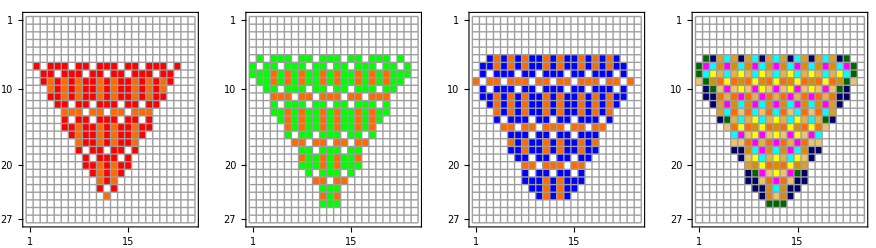

```mathematica
Block[{l=10},GraphicsGrid[{
{MatrixPlot[ (LCaCbZero["bins"])[[l-1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[LCaCbZero["bins"][[l,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[LCaCbZero["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[LCaCbZero["bins"][[l-1,All,All]]+2 LCaCbZero["bins"][[l,All,All]]+4 LCaCbZero["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}]
]
```

```mathematica
Max[uLCaCb[0]["bins"]]
```

0

```mathematica
Do[uLCaCb[θ]=AnalyseTransform[ fRs[θ],scale["LCaCb","nLCaCb"][θ] scale["nLCaCb","fRs"][θ],15],{θ,0,Pi/2,Pi/24}];
```

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 | 5 √6
-15/(√2) | 15/(√2))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
Min[√(2/3) Cos[π/24] (15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24]))),√(2/3) Cos[π/24] (15+15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24])))] | 5 √6 Cos[π/24]
Min[√(2/3) Cos[π/8] (15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8]))),√(2/3) Cos[π/8] (15+15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8])))] | 5 √6 Cos[π/8])

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
Min[((1+√3) (15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3),((1+√3) (15+15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3)] | 5/2 √3 (1+√3)
Min[((1+√3) (15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3),((1+√3) (15+15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3)] | 5/2 √3 (1+√3))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
Min[√(2/3) Cos[π/8] (15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8]))),√(2/3) Cos[π/8] (15+15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8])))] | 5 √6 Cos[π/8]
Min[√(2/3) Cos[π/24] (15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24]))),√(2/3) Cos[π/24] (15+15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24])))] | 5 √6 Cos[π/24])

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-15/(√2) | 15/(√2)
-5 √6 | 5 √6)

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 Cos[π/8] | √(2/3) Cos[π/8] (15/2 (1+√3 Tan[π/8])+15 (1+1/2 (-1-√3 Tan[π/8])))
Min[√(2/3) Cos[π/24] (15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24]))),√(2/3) Cos[π/24] (15+15/2 (-1-√3 Tan[π/24])+15 (-1+1/2 (1+√3 Tan[π/24])))] | 5 √6 Cos[π/24])

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5/2 √3 (1+√3) | ((1+√3) (15/2 (1+√3 (2-√3))+15 (1+1/2 (-1-√3 (2-√3)))))/(2 √3)
Min[((1+√3) (15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3),((1+√3) (15+15/2 (-1-√3 (2-√3))+15 (-1+1/2 (1+√3 (2-√3)))))/(2 √3)] | 5/2 √3 (1+√3))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 Cos[π/24] | √(2/3) Cos[π/24] (15/2 (1+√3 Tan[π/24])+15 (1+1/2 (-1-√3 Tan[π/24])))
Min[√(2/3) Cos[π/8] (15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8]))),√(2/3) Cos[π/8] (15+15/2 (-1-√3 Tan[π/8])+15 (-1+1/2 (1+√3 Tan[π/8])))] | 5 √6 Cos[π/8])

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 | 5 √6
-15/(√2) | 15/(√2))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 Cos[π/24] | √(2/3) Cos[π/24] (15/2 (1+√3 Tan[π/24])+15 (1+1/2 (-1-√3 Tan[π/24])))
-5 √6 Cos[π/8] | √(2/3) Cos[π/8] (15/2 (1+√3 Tan[π/8])+15 (1+1/2 (-1-√3 Tan[π/8]))))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5/2 √3 (1+√3) | ((1+√3) (15/2 (1+√3 (2-√3))+15 (1+1/2 (-1-√3 (2-√3)))))/(2 √3)
-5/2 √3 (1+√3) | ((1+√3) (15/2 (1+√3 (2-√3))+15 (1+1/2 (-1-√3 (2-√3)))))/(2 √3))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-5 √6 Cos[π/8] | √(2/3) Cos[π/8] (15/2 (1+√3 Tan[π/8])+15 (1+1/2 (-1-√3 Tan[π/8])))
-5 √6 Cos[π/24] | √(2/3) Cos[π/24] (15/2 (1+√3 Tan[π/24])+15 (1+1/2 (-1-√3 Tan[π/24]))))

Dimensions[pts] = {16,16,16,3}

Dimensions[orderedPts] = {4096,3}

Range = (0 | 15 √3
-15/(√2) | 15/(√2)
-5 √6 | 5 √6)

```mathematica
Block[{l=10},GraphicsGrid[{
{MatrixPlot[ uLCaCb[0]["bins"][[l-1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[uLCaCb[0]["bins"][[l,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[uLCaCb[0]["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[uLCaCb[0]["bins"][[l-1,All,All]]+2 uLCaCb[0]["bins"][[l,All,All]]+4 uLCaCb[0]["bins"][[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}]
]
```

-Graphics-

```mathematica
Clear[S,T,LCaCb16,orderedLCaCb16,range,indx,shift,dim,bins,pnts]
Block[{θ=0.2,n=15},
S=  scale["LCaCb","nLCaCb"][θ] scale["nLCaCb","fRs"][θ];
 S = {1,1,1}; 
T= fRs[θ];
LCaCb16 = Table[S(T.{r,g,b}),{r,0,n},{g,0,n},{b,0,n}];
orderedLCaCb16=Sort[Flatten[LCaCb16,2]];
Print["Dimensions[LCaCb16] = ",Dimensions[LCaCb16]];
Print["Dimensions[orderedLCaCb16] = ",Dimensions[orderedLCaCb16]];
range={{Min[LCaCb16[[All,All,All,1]]],Max[LCaCb16[[All,All,All,1]]]},{Min[LCaCb16[[All,All,All,2]]],Max[LCaCb16[[All,All,All,2]]]},{Min[LCaCb16[[All,All,All,3]]],Max[LCaCb16[[All,All,All,3]]]}};
Print["Range = ",MatrixForm[range]];
indx=Flatten[Table[Floor[LCaCb16[[r,g,b,All]]],{r,1,n+1},{g,1,n+1},{b,1,n+1}],2];
shift={1-Min[indx[[All,1]]],1-Min[indx[[All,2]]],1-Min[indx[[All,3]]]};
dim={Ceiling@Max[LCaCb16[[All,All,All,1]]]+shift[[1]],Ceiling@Max[LCaCb16[[All,All,All,2]]]+shift[[2]],Ceiling@Max[LCaCb16[[All,All,All,3]]]+shift[[3]]};
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Do[Part[bins,indx[[i,1]]+shift[[1]],indx[[i,2]]+shift[[2]],indx[[i,3]]+shift[[3]]]++,{i,1,Length[indx]}];

]
```

Dimensions[LCaCb16] = {16,16,16,3}

Dimensions[orderedLCaCb16] = {4096,3}

Range = (0. | 45.
-15. | 15.
-15. | 15.)

```mathematica
AnalysePoints[pts_]
```

```mathematica
Clear[AnalysePoints]
AnalysePoints[pts_]:=Module[{analysed},
analysed["vals"]={Union[N[pts[[All,1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[N[pts[[All,2]]],SameTest->(Abs[#1-#2]≤0.001&)],Union[N[pts[[All,3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
analysed["diffs"]=Flatten[{
Union[Rest[analysed["vals"][[1]]]-Most[analysed["vals"][[1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[2]]]-Most[analysed["vals"][[2]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[3]]]-Most[analysed["vals"][[3]]],SameTest->(Abs[#1-#2]≤0.001&)]}];
 analysed
]
```

```mathematica
Manipulate[GraphicsGrid[{
{MatrixPlot[ bins[[All,All,Cb-1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[bins[[All,All,Cb]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[bins[[All,All,Cb+1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[bins[[All,All,Cb-1]]+2 bins[[All,All,Cb]]+4 bins[[All,All,Cb+1]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}],{{Cb,2},2,Dimensions[bins][[3]],1}]
```

```mathematica
Manipulate[GraphicsGrid[{
{MatrixPlot[ bins[[All,Ca-1,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[bins[[All,Ca,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[bins[[All,Ca+1,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[bins[[All,Ca-1,All]]+2 bins[[All,Ca,All]]+4 bins[[All,Ca+1,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}],{{Ca,2},2,Dimensions[bins][[2]],1}]
```

```mathematica
Manipulate[GraphicsGrid[{
{MatrixPlot[ bins[[l-1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[bins[[l,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[bins[[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[bins[[l-1,All,All]]+2 bins[[l,All,All]]+4 bins[[l+1,All,All]],ImageSize->200,Mesh->All,ColorRules->{0->White,1->RGBColor[0.4,0,0],2-> RGBColor[0,0.4,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,0.4],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] }}],{{l,2},2,Dimensions[bins][[1]],1}]
```

```mathematica
N[15 scale["LCaCb","nLCaCb"][0]]
N[2 range]
```

{25.9808,24.4949,21.2132}

{{0.,90.},{-30.,30.},{-30.,30.}}

```mathematica
AppendTo[$Path,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats"]
```

{/Applications/Mathematica 2.app/AddOns/Applications,/Applications/Mathematica 2.app/SystemFiles/Links,/Users/jaspershemilt/Library/Mathematica/Kernel,/Users/jaspershemilt/Library/Mathematica/Autoload,/Users/jaspershemilt/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/jaspershemilt,/Applications/Mathematica 2.app/AddOns/Packages,/Applications/Mathematica 2.app/AddOns/LegacyPackages,/Applications/Mathematica 2.app/SystemFiles/Autoload,/Applications/Mathematica 2.app/AddOns/Autoload,/Applications/Mathematica 2.app/AddOns/Applications,/Applications/Mathematica 2.app/AddOns/ExtraPackages,/Applications/Mathematica 2.app/SystemFiles/Kernel/Packages,/Applications/Mathematica 2.app/Documentation/English/System,/Applications/Mathematica 2.app/SystemFiles/Data/ICC,/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/Mathematica/old/,/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/Mathematica/old/,/Users/jaspershemilt/Developer/projects/Color-Space-Stats,/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats}

## Import Data

```mathematica
data=Flatten[Table[{r Cos[t],r Sin[t],Sinc[r]},{r,0,10,0.5},{t,0,2Pi,0.1}],1];
```

```mathematica
speckle=Import["speckle.mat"][[1]];
```

```mathematica
eq=({{0≤y/(√3)-√(2/3) b Cos[π/6+θ]-√(2/3) a Sin[π/6+θ]≤255}, {0≤y/(√3)+√(2/3) a Cos[θ]-√(2/3) b Sin[θ]≤255}, {0≤y/(√3)+√(2/3) b Cos[π/6-θ]-√(2/3) a Sin[π/6-θ]≤255}});
InsideCubeQ[{y_,a_,b_}]:=Evaluate[Reduce[Simplify[eq/.{θ->0}],{y,a,b}]]
```

```mathematica
speckle=Select[speckle,InsideCubeQ];
```

```mathematica
Save[NotebookDirectory[]<>"speckle.nb",speckle]
```

```mathematica
speckle=speckle[[1]];
```

```mathematica
ListPointPlot3D[speckle]
```

ListPointPlot3D[$Failed⟦1⟧]

```mathematica
speckle[[1]]
```

```mathematica
Head[speckle]
```

List

```mathematica
speckle[[1,10]]
```

{10.,1.,1.}

```mathematica
Length[speckle]
```

3533040

```mathematica
mapYab16=Import["Transform/mapYab16.mat"][[1]];
```

```mathematica
Dimensions[mapYab16]
```

{3,16,16,16}

```mathematica
redLines=Flatten[Table[mapYab16[[All,r,g,b]],{g,1,16},{b,1,16},{r,1,16}],1];
greenLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,16},{b,1,16},{g,1,16}],1];
blueLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,16},{g,1,16},{b,1,16}],1];
dRanges={{Min[mapYab16[[1,All,All,All]]],Max[mapYab16[[1,All,All,All]]]},
{Min[mapYab16[[2,All,All,All]]],Max[mapYab16[[2,All,All,All]]]},
{Min[mapYab16[[3,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}};
dLengths={-Min[mapYab16[[1,All,All,All]]]+Max[mapYab16[[1,All,All,All]]],
-Min[mapYab16[[2,All,All,All]]]+Max[mapYab16[[2,All,All,All]]],
-Min[mapYab16[[3,All,All,All]]]+Max[mapYab16[[3,All,All,All]]]};
ranges={{Floor[Min[mapYab16[[1,All,All,All]]]],Ceiling[Max[mapYab16[[1,All,All,All]]]]},
{Floor[Min[mapYab16[[2,All,All,All]]]],Ceiling[Max[mapYab16[[2,All,All,All]]]]},
{Floor[Min[mapYab16[[3,All,All,All]]]],Ceiling[Max[mapYab16[[3,All,All,All]]]]}};
yLine=Flatten[{Black,Table[Line[{{ranges[[1,1]],a-0.5,b-0.5},{ranges[[1,2]],a-0.5,b-0.5}}],{a,ranges[[2,1]],ranges[[2,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
aLine=Flatten[{Black,Table[Line[{{y-0.5,ranges[[2,1]],b-0.5},{y-0.5,ranges[[2,2]],b-0.5}}],{y,ranges[[1,1]],ranges[[1,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
bLine=Flatten[{Black,Table[Line[{{y-0.5,a-0.5,ranges[[3,1]]},{y-0.5,a-0.5,ranges[[3,2]]}}],{y,ranges[[1,1]],ranges[[1,2]]+1},{a,ranges[[2,1]],ranges[[2,2]]+1}]}];
```

```mathematica
ListPointPlot3D[redLines]
```

-Graphics3D-

```mathematica
mapYab16[[All,1,1,1]]
```

{-0.133975,12.5639,10.8137}

```mathematica
redLine=Flatten[{Red,MapThread[Line[{#1,#2}]&,{redLines[[All,1,All]],redLines[[All,-1,All]]}]}];
blueLine=Flatten[{Blue,MapThread[Line[{#1,#2}]&,{blueLines[[All,1,All]],blueLines[[All,-1,All]]}]}];
greenLine=Flatten[{Green,MapThread[Line[{#1,#2}]&,{greenLines[[All,1,All]],greenLines[[All,-1,All]]}]}];
grfx={redLine,blueLine,greenLine,yLine,aLine,bLine};
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0},Axes->True,Ticks->All]
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
dRanges
```

{{0.,25.9808},{0.816497,25.3114},{0.707107,21.9203}}

```mathematica
2^4
```

16

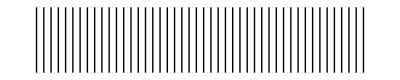

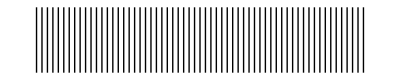

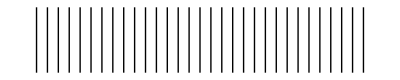

{0.577778,0.577778,0.577778,0.577778,0.577778,0.577778,0.577778}

{0.416667,0.416667,0.416667,0.416667}

{0.733333,0.733333,0.733333,0.733333}

```mathematica
yPts=Union[Flatten[mapYab16[[1,All,All,All]]]];
aPts=Union[Flatten[mapYab16[[2,All,All,All]]]];
bPts=Union[Flatten[mapYab16[[3,All,All,All]]]];
Graphics[Map[Line[{{#,0},{#,1}}]&,yPts]]
Graphics[Map[Line[{{#,0},{#,1}}]&,aPts]]
Graphics[Map[Line[{{#,0},{#,1}}]&,bPts]]
Union[Rest[yPts]-Most[yPts]]
Union[Rest[aPts]-Most[aPts]]
Union[Rest[bPts]-Most[bPts]]
```

```mathematica
Dimensions[mapYab16]
```

{3,16,16,16}

```mathematica
mapYab16[[All,10,11,12]]
```

{17.3333,13.75,10.2667}

```mathematica
Extract[mapYab16,{1;;3,1,2,3}]
```

Extract[{{1},{{{12.5639,13.3804,14.1969,15.0134,15.8299,16.6464,4,20.7289,21.5454,22.3619,23.1784,23.9949,24.8114},14,{1}},14,{1}},{{1},14,{1}}},1]
 |  |  |  |

```mathematica
pos=ReleaseHold[Map[Hold[Sequence][Prepend[#,1],Prepend[#,2],Prepend[#,3]]&,Position[mapYab16[[2,All,All,All]],13.75,4]]]
Extract[mapYab16,pos]
```

{{1,1,2,3},{2,1,2,3},{3,1,2,3},{1,1,4,4},{2,1,4,4},{3,1,4,4},{1,1,6,5},{2,1,6,5},{3,1,6,5},{1,1,8,6},{2,1,8,6},{3,1,8,6},{1,1,10,7},{2,1,10,7},{3,1,10,7},{1,1,12,8},{2,1,12,8},{3,1,12,8},{1,1,14,9},{2,1,14,9},{3,1,14,9},{1,1,16,10},{2,1,16,10},{3,1,16,10},{1,2,1,3},{2,2,1,3},{3,2,1,3},{1,2,3,4},{2,2,3,4},{3,2,3,4},{1,2,5,5},{2,2,5,5},{3,2,5,5},{1,2,7,6},{2,2,7,6},{3,2,7,6},{1,2,9,7},{2,2,9,7},{3,2,9,7},{1,2,11,8},{2,2,11,8},{3,2,11,8},{1,2,13,9},{2,2,13,9},{3,2,13,9},{1,2,15,10},{2,2,15,10},{3,2,15,10},{1,3,2,4},{2,3,2,4},{3,3,2,4},{1,3,4,5},{2,3,4,5},{3,3,4,5},{1,3,6,6},{2,3,6,6},{3,3,6,6},{1,3,8,7},{2,3,8,7},{3,3,8,7},{1,3,10,8},{2,3,10,8},{3,3,10,8},{1,3,12,9},{2,3,12,9},{3,3,12,9},{1,3,14,10},{2,3,14,10},{3,3,14,10},{1,3,16,11},{2,3,16,11},{3,3,16,11},{1,4,1,4},{2,4,1,4},{3,4,1,4},{1,4,3,5},{2,4,3,5},{3,4,3,5},{1,4,5,6},{2,4,5,6},{3,4,5,6},{1,4,7,7},{2,4,7,7},{3,4,7,7},{1,4,9,8},{2,4,9,8},{3,4,9,8},{1,4,11,9},{2,4,11,9},{3,4,11,9},{1,4,13,10},{2,4,13,10},{3,4,13,10},{1,4,15,11},{2,4,15,11},{3,4,15,11},{1,5,2,5},{2,5,2,5},{3,5,2,5},{1,5,4,6},{2,5,4,6},{3,5,4,6},{1,5,6,7},{2,5,6,7},{3,5,6,7},{1,5,8,8},{2,5,8,8},{3,5,8,8},{1,5,10,9},{2,5,10,9},{3,5,10,9},{1,5,12,10},{2,5,12,10},{3,5,12,10},{1,5,14,11},{2,5,14,11},{3,5,14,11},{1,5,16,12},{2,5,16,12},{3,5,16,12},{1,6,1,5},{2,6,1,5},{3,6,1,5},{1,6,3,6},{2,6,3,6},{3,6,3,6},{1,6,5,7},{2,6,5,7},{3,6,5,7},{1,6,7,8},{2,6,7,8},{3,6,7,8},{1,6,9,9},{2,6,9,9},{3,6,9,9},{1,6,11,10},{2,6,11,10},{3,6,11,10},{1,6,13,11},{2,6,13,11},{3,6,13,11},{1,6,15,12},{2,6,15,12},{3,6,15,12},{1,7,2,6},{2,7,2,6},{3,7,2,6},{1,7,4,7},{2,7,4,7},{3,7,4,7},{1,7,6,8},{2,7,6,8},{3,7,6,8},{1,7,8,9},{2,7,8,9},{3,7,8,9},{1,7,10,10},{2,7,10,10},{3,7,10,10},{1,7,12,11},{2,7,12,11},{3,7,12,11},{1,7,14,12},{2,7,14,12},{3,7,14,12},{1,7,16,13},{2,7,16,13},{3,7,16,13},{1,8,1,6},{2,8,1,6},{3,8,1,6},{1,8,3,7},{2,8,3,7},{3,8,3,7},{1,8,5,8},{2,8,5,8},{3,8,5,8},{1,8,7,9},{2,8,7,9},{3,8,7,9},{1,8,9,10},{2,8,9,10},{3,8,9,10},{1,8,11,11},{2,8,11,11},{3,8,11,11},{1,8,13,12},{2,8,13,12},{3,8,13,12},{1,8,15,13},{2,8,15,13},{3,8,15,13},{1,9,2,7},{2,9,2,7},{3,9,2,7},{1,9,4,8},{2,9,4,8},{3,9,4,8},{1,9,6,9},{2,9,6,9},{3,9,6,9},{1,9,8,10},{2,9,8,10},{3,9,8,10},{1,9,10,11},{2,9,10,11},{3,9,10,11},{1,9,12,12},{2,9,12,12},{3,9,12,12},{1,9,14,13},{2,9,14,13},{3,9,14,13},{1,9,16,14},{2,9,16,14},{3,9,16,14},{1,10,1,7},{2,10,1,7},{3,10,1,7},{1,10,3,8},{2,10,3,8},{3,10,3,8},{1,10,5,9},{2,10,5,9},{3,10,5,9},{1,10,7,10},{2,10,7,10},{3,10,7,10},{1,10,9,11},{2,10,9,11},{3,10,9,11},{1,10,11,12},{2,10,11,12},{3,10,11,12},{1,10,13,13},{2,10,13,13},{3,10,13,13},{1,10,15,14},{2,10,15,14},{3,10,15,14},{1,11,2,8},{2,11,2,8},{3,11,2,8},{1,11,4,9},{2,11,4,9},{3,11,4,9},{1,11,6,10},{2,11,6,10},{3,11,6,10},{1,11,8,11},{2,11,8,11},{3,11,8,11},{1,11,10,12},{2,11,10,12},{3,11,10,12},{1,11,12,13},{2,11,12,13},{3,11,12,13},{1,11,14,14},{2,11,14,14},{3,11,14,14},{1,11,16,15},{2,11,16,15},{3,11,16,15},{1,12,1,8},{2,12,1,8},{3,12,1,8},{1,12,3,9},{2,12,3,9},{3,12,3,9},{1,12,5,10},{2,12,5,10},{3,12,5,10},{1,12,7,11},{2,12,7,11},{3,12,7,11},{1,12,9,12},{2,12,9,12},{3,12,9,12},{1,12,11,13},{2,12,11,13},{3,12,11,13},{1,12,13,14},{2,12,13,14},{3,12,13,14},{1,12,15,15},{2,12,15,15},{3,12,15,15},{1,13,2,9},{2,13,2,9},{3,13,2,9},{1,13,4,10},{2,13,4,10},{3,13,4,10},{1,13,6,11},{2,13,6,11},{3,13,6,11},{1,13,8,12},{2,13,8,12},{3,13,8,12},{1,13,10,13},{2,13,10,13},{3,13,10,13},{1,13,12,14},{2,13,12,14},{3,13,12,14},{1,13,14,15},{2,13,14,15},{3,13,14,15},{1,13,16,16},{2,13,16,16},{3,13,16,16},{1,14,1,9},{2,14,1,9},{3,14,1,9},{1,14,3,10},{2,14,3,10},{3,14,3,10},{1,14,5,11},{2,14,5,11},{3,14,5,11},{1,14,7,12},{2,14,7,12},{3,14,7,12},{1,14,9,13},{2,14,9,13},{3,14,9,13},{1,14,11,14},{2,14,11,14},{3,14,11,14},{1,14,13,15},{2,14,13,15},{3,14,13,15},{1,14,15,16},{2,14,15,16},{3,14,15,16},{1,15,2,10},{2,15,2,10},{3,15,2,10},{1,15,4,11},{2,15,4,11},{3,15,4,11},{1,15,6,12},{2,15,6,12},{3,15,6,12},{1,15,8,13},{2,15,8,13},{3,15,8,13},{1,15,10,14},{2,15,10,14},{3,15,10,14},{1,15,12,15},{2,15,12,15},{3,15,12,15},{1,15,14,16},{2,15,14,16},{3,15,14,16},{1,16,1,10},{2,16,1,10},{3,16,1,10},{1,16,3,11},{2,16,3,11},{3,16,3,11},{1,16,5,12},{2,16,5,12},{3,16,5,12},{1,16,7,13},{2,16,7,13},{3,16,7,13},{1,16,9,14},{2,16,9,14},{3,16,9,14},{1,16,11,15},{2,16,11,15},{3,16,11,15},{1,16,13,16},{2,16,13,16},{3,16,13,16}}

{2.,13.75,10.2667,4.,13.75,8.8,6.,13.75,7.33333,8.,13.75,5.86667,10.,13.75,4.4,12.,13.75,2.93333,14.,13.75,1.46667,16.,13.75,0.,2.,13.75,11.7333,4.,13.75,10.2667,6.,13.75,8.8,8.,13.75,7.33333,10.,13.75,5.86667,12.,13.75,4.4,14.,13.75,2.93333,16.,13.75,1.46667,4.,13.75,11.7333,6.,13.75,10.2667,8.,13.75,8.8,10.,13.75,7.33333,12.,13.75,5.86667,14.,13.75,4.4,16.,13.75,2.93333,18.,13.75,1.46667,4.,13.75,13.2,6.,13.75,11.7333,8.,13.75,10.2667,10.,13.75,8.8,12.,13.75,7.33333,14.,13.75,5.86667,16.,13.75,4.4,18.,13.75,2.93333,6.,13.75,13.2,8.,13.75,11.7333,10.,13.75,10.2667,12.,13.75,8.8,14.,13.75,7.33333,16.,13.75,5.86667,18.,13.75,4.4,20.,13.75,2.93333,6.,13.75,14.6667,8.,13.75,13.2,10.,13.75,11.7333,12.,13.75,10.2667,14.,13.75,8.8,16.,13.75,7.33333,18.,13.75,5.86667,20.,13.75,4.4,8.,13.75,14.6667,10.,13.75,13.2,12.,13.75,11.7333,14.,13.75,10.2667,16.,13.75,8.8,18.,13.75,7.33333,20.,13.75,5.86667,22.,13.75,4.4,8.,13.75,16.1333,10.,13.75,14.6667,12.,13.75,13.2,14.,13.75,11.7333,16.,13.75,10.2667,18.,13.75,8.8,20.,13.75,7.33333,22.,13.75,5.86667,10.,13.75,16.1333,12.,13.75,14.6667,14.,13.75,13.2,16.,13.75,11.7333,18.,13.75,10.2667,20.,13.75,8.8,22.,13.75,7.33333,24.,13.75,5.86667,10.,13.75,17.6,12.,13.75,16.1333,14.,13.75,14.6667,16.,13.75,13.2,18.,13.75,11.7333,20.,13.75,10.2667,22.,13.75,8.8,24.,13.75,7.33333,12.,13.75,17.6,14.,13.75,16.1333,16.,13.75,14.6667,18.,13.75,13.2,20.,13.75,11.7333,22.,13.75,10.2667,24.,13.75,8.8,26.,13.75,7.33333,12.,13.75,19.0667,14.,13.75,17.6,16.,13.75,16.1333,18.,13.75,14.6667,20.,13.75,13.2,22.,13.75,11.7333,24.,13.75,10.2667,26.,13.75,8.8,14.,13.75,19.0667,16.,13.75,17.6,18.,13.75,16.1333,20.,13.75,14.6667,22.,13.75,13.2,24.,13.75,11.7333,26.,13.75,10.2667,28.,13.75,8.8,14.,13.75,20.5333,16.,13.75,19.0667,18.,13.75,17.6,20.,13.75,16.1333,22.,13.75,14.6667,24.,13.75,13.2,26.,13.75,11.7333,28.,13.75,10.2667,16.,13.75,20.5333,18.,13.75,19.0667,20.,13.75,17.6,22.,13.75,16.1333,24.,13.75,14.6667,26.,13.75,13.2,28.,13.75,11.7333,16.,13.75,22.,18.,13.75,20.5333,20.,13.75,19.0667,22.,13.75,17.6,24.,13.75,16.1333,26.,13.75,14.6667,28.,13.75,13.2}

```mathematica
n=16;
dim={Max[mapYab16[[1,All,All,All]]],Max[mapYab16[[2,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Dimensions[bins]
indx=Flatten[Table[Round[mapYab16[[All,r,g,b]]]+1,{r,1,n},{g,1,n},{b,1,n}],2];
{Max[indx[[All,1]]],Max[indx[[All,2]]],Max[indx[[All,3]]]}
Do[Part[bins,indx[[i,1]],indx[[i,2]],indx[[i,3]]]++,{i,1,Length[indx]}];
```

{25.8468,24.8114,21.4203}

{26,25,22}

{27,26,22}

```mathematica
{Max[indx[[All,1]]],Max[indx[[All,2]]],Max[indx[[All,3]]]}
```

{31,26,23}

```mathematica
Part[bins,indx[[2,1]],indx[[2,2]],indx[[2,3]]]++
```

4

{{1,13,12},{2,14,12},{2,15,12},{3,16,12},{4,17,12},{4,18,12},{5,19,12},{6,19,12},{6,20,12},{7,21,12},{8,22,12},{8,23,12},{9,23,12},{10,24,12},{10,25,12},{11,26,12},{2,13,11},{2,14,11},4061,{30,14,13},{21,1,12},{22,2,12},{22,3,12},{23,3,12},{24,4,12},{24,5,12},{25,6,12},{26,7,12},{26,8,12},{27,9,12},{28,9,12},{28,10,12},{29,11,12},{30,12,12},{30,13,12},{31,13,12}}
 |  |  |  |

```mathematica
n=2^4;
mapYab16=Import["Transform/mapYab16.mat"][[1]];
redLines=Flatten[Table[mapYab16[[All,r,g,b]],{g,1,n},{b,1,n},{r,1,n}],1];
greenLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,n},{b,1,n},{g,1,n}],1];
blueLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,n},{g,1,n},{b,1,n}],1];
dRanges={{Min[mapYab16[[1,All,All,All]]],Max[mapYab16[[1,All,All,All]]]},
{Min[mapYab16[[2,All,All,All]]],Max[mapYab16[[2,All,All,All]]]},
{Min[mapYab16[[3,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}};
dLengths={-Min[mapYab16[[1,All,All,All]]]+Max[mapYab16[[1,All,All,All]]],
-Min[mapYab16[[2,All,All,All]]]+Max[mapYab16[[2,All,All,All]]],
-Min[mapYab16[[3,All,All,All]]]+Max[mapYab16[[3,All,All,All]]]};
ranges={{Floor[Min[mapYab16[[1,All,All,All]]]],Ceiling[Max[mapYab16[[1,All,All,All]]]]},
{Floor[Min[mapYab16[[2,All,All,All]]]],Ceiling[Max[mapYab16[[2,All,All,All]]]]},
{Floor[Min[mapYab16[[3,All,All,All]]]],Ceiling[Max[mapYab16[[3,All,All,All]]]]}};
yLine=Flatten[{Black,Table[Line[{{ranges[[1,1]],a,b},{ranges[[1,2]],a,b}}],{a,ranges[[2,1]],ranges[[2,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
aLine=Flatten[{Black,Table[Line[{{y,ranges[[2,1]],b},{y,ranges[[2,2]],b}}],{y,ranges[[1,1]],ranges[[1,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
bLine=Flatten[{Black,Table[Line[{{y,a,ranges[[3,1]]},{y,a,ranges[[3,2]]}}],{y,ranges[[1,1]],ranges[[1,2]]},{a,ranges[[2,1]],ranges[[2,2]]}]}];
redLine=Flatten[{Red,MapThread[Line[{#1,#2}]&,{redLines[[All,1,All]],redLines[[All,-1,All]]}]}];
blueLine=Flatten[{Blue,MapThread[Line[{#1,#2}]&,{blueLines[[All,1,All]],blueLines[[All,-1,All]]}]}];
greenLine=Flatten[{Green,MapThread[Line[{#1,#2}]&,{greenLines[[All,1,All]],greenLines[[All,-1,All]]}]}];
grfx={redLine,blueLine,greenLine,yLine,aLine,bLine};
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0},PlotRange->{All,All,{7,8}},Axes->True]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0},PlotRange->{All,{7,8},All},Axes->True]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},PlotRange->{{7,8},All,All},Axes->True]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
GraphicsRow[{Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0},PlotRange->{All,All,{7,8}}],Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0},PlotRange->{All,{7,8},All}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},PlotRange->{{7,8},All,All}]}]
```

-Graphics-

```mathematica
speck16Bin=Import["Transform/speck16_Bin.mat"][[1]];
Dimensions[speck16Bin]
Max[speck16Bin]
```

{24,28,27}

5.

```mathematica
Max[bins]
```

2

```mathematica
GraphicsCubeOpts
```

```mathematica
Count[Flatten[bins],n_/;n==2]
```

868

```mathematica
Graphics3D[{Raster3D[bins/Max[bins],ColorFunction->"GrayLevelOpacity"]},GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Dimensions[bins]
```

{26,26,22}

```mathematica
Dimensions[mapYab16[[All,13,All,All]]]
```

{3,16,16}

```mathematica
orderedYab16=Sort[Flatten[Transpose[mapYab16,{4,1,2,3}],2]];
```

```mathematica
LVals=Union[orderedYab16[[All,1]]]
Length[LVals]
CaVals=Union[orderedYab16[[All,2]]]
Length[CaVals]
CbVals=Union[orderedYab16[[All,3]]]
Length[CbVals]
```

{-0.133975,0.443376,1.02073,1.59808,2.17543,2.75278,3.33013,3.90748,4.48483,5.06218,5.63953,6.21688,6.79423,7.37158,7.94893,8.52628,9.10363,9.68098,10.2583,10.8357,11.413,11.9904,12.5677,13.1451,13.7224,14.2998,14.8771,15.4545,16.0318,16.6092,17.1865,17.7639,18.3412,18.9186,19.4959,20.0733,20.6506,21.228,21.8053,22.3827,22.96,23.5374,24.1147,24.6921,25.2694,25.8468}

46

{0.316497,0.724745,1.13299,1.54124,1.94949,2.35774,2.76599,3.17423,3.58248,3.99073,4.39898,4.80723,5.21548,5.62372,6.03197,6.44022,6.84847,7.25672,7.66497,8.07321,8.48146,8.88971,9.29796,9.70621,10.1145,10.5227,10.931,11.3392,11.7474,12.1557,12.5639,12.9722,13.3804,13.7887,14.1969,14.6052,15.0134,15.4217,15.8299,16.2382,16.6464,17.0547,17.4629,17.8712,18.2794,18.6877,19.0959,19.5042,19.9124,20.3207,20.7289,21.1372,21.5454,21.9537,22.3619,22.7702,23.1784,23.5866,23.9949,24.4031,24.8114}

61

{0.207107,0.914214,1.62132,2.32843,3.03553,3.74264,4.44975,5.15685,5.86396,6.57107,7.27817,7.98528,8.69239,9.39949,10.1066,10.8137,11.5208,12.2279,12.935,13.6421,14.3492,15.0563,15.7635,16.4706,17.1777,17.8848,18.5919,19.299,20.0061,20.7132,21.4203}

31

```mathematica
LCaCbSteps=Flatten[{Union[Rest[LVals]-Most[LVals],SameTest->(Abs[#1-#2]≤0.0000001&)],
Union[Rest[CaVals]-Most[CaVals],SameTest->(Abs[#1-#2]≤0.0000001&)],
Union[Rest[CbVals]-Most[CbVals],SameTest->(Abs[#1-#2]≤0.0000001&)]}]
Block[{vars=(1/LCaCbSteps^2)},{Sqrt[1/Round[vars[[1]]]],Sqrt[1/Round[vars[[2]]]],Sqrt[1/Round[vars[[3]]]]}]
```

{0.57735,0.408248,0.707107}

{1/(√3),1/(√6),1/(√2)}

```mathematica
Definition[scale]
```

scale[nLCaCb,LCaCb][θ:Except[_String],θ2m1_,θ2_]:=scaleFun[nLCaCb,LCaCb][θ,θ2m1,θ2]
 
scale[nLCaCb,LCaCb][θ:Except[_String]]:=scaleFun[nLCaCb,LCaCb][θ,Mod[θ-π/6,π/3],Mod[θ,π/3]]
 
scale[LCaCb,nLCaCb][θ:Except[_String],θ2m1_,θ2_]:=scaleFun[LCaCb,nLCaCb][θ,θ2m1,θ2]
 
scale[LCaCb,nLCaCb][θ:Except[_String]]:=scaleFun[LCaCb,nLCaCb][θ,Mod[θ-π/6,π/3],Mod[θ,π/3]]
 
scale[LCaCb,rR][θ:Except[_String]]={1/(√3),√(2/3),√(2/3)}
 
scale[LCaCb,rR][_String]=rS
 
scale[rR,fR][θ:Except[_String]]:=Piecewise[{{{1,Cos[θ],Cos[π/6-θ]}, 0≤Mod[θ,π]<π/6}, {{1,-Sin[π/6+θ],Cos[π/6-θ]}, π/6≤Mod[θ,π]<π/3}, {{1,-Sin[π/6+θ],-Sin[θ]}, π/3≤Mod[θ,π]<π/2}, {{1,-Sin[π/6-θ],-Sin[θ]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,-Sin[π/6-θ],-Cos[π/6+θ]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,Cos[θ],-Cos[π/6+θ]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]
 
scale[rR,fRs][θ:Except[_String]]:={1,Cos[Mod[θ-π/6,π/3]-π/6],Cos[Mod[θ,π/3]-π/6]}
 
scale[qR,fR][θ:Except[_String],n_:8]:={1,2^(n-2),2^(n-2)}
 
scale[fR,qR][θ:Except[_String],n_:8]:={1,2^(2-n),2^(2-n)}
 
scale[qRs,fRs][θ:Except[_String],n_:8]:={1,2^(n-2),2^(n-2)}
 
scale[fRs,qRs][θ:Except[_String],n_:8]:={1,2^(2-n),2^(2-n)}
 
scale[nLCaCb,fRs][θ:Except[_String]]:={1/3,1/2,1/2}
 
scale[fRs,nLCaCb][θ:Except[_String]]:={3,2,2}
 
scale[nLCaCb,qRs][θ:Except[_String]]:={1/3,2^(1-n),2^(1-n)}
 
scale[qRs,nLCaCb][θ:Except[_String]]:={3,2^(3-n),2^(3-n)}
 
scale[nLCaCb,rR][θ:Except[_String]]:={1/3,1/2 Sec[π/6-Mod[-π/6+θ,π/3]],1/2 Sec[π/6-Mod[θ,π/3]]}
 
scale[rR,qR][θ:Except[_String],n_:8]:=Piecewise[{{{1,-(2^(2-n) Sin[π/6+θ]),-(2^(2-n) Cos[π/6+θ])}, 0≤Mod[θ,π/2]<π/6}, {{1,2^(2-n) Cos[θ],-(2^(2-n) Sin[θ])}, π/6≤Mod[θ,π/2]<π/3}, {{1,-(2^(2-n) Sin[π/6-θ]),2^(2-n) Cos[π/6-θ]}, π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]
 
scale[qR,rR][θ:Except[_String],n_:8]:=Piecewise[{{{1,-(2^(-2+n) Csc[π/6+θ]),-(2^(-2+n) Sec[π/6+θ])}, 0≤Mod[θ,π/2]<π/6}, {{1,2^(-2+n) Sec[θ],-(2^(-2+n) Csc[θ])}, π/6≤Mod[θ,π/2]<π/3}, {{1,-(2^(-2+n) Csc[π/6-θ]),2^(-2+n) Sec[π/6-θ]}, π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]
 
scale[nLCaCb,qRs][θ:Except[_String],n_:8]:={1/3,2^(1-n),2^(1-n)}
 
scale[qRs,nLCaCb][θ:Except[_String],n_:8]:={3,2^(3-n),2^(3-n)}
 
scale/:MakeBoxes[scale[fR,qR],TraditionalForm]=Format[qS,TraditionalForm]
 
scale/:MakeBoxes[scale[fRs,nLCaCb],TraditionalForm]=Format[Superscript[Subscript[S,q],-1],TraditionalForm]
 
scale/:MakeBoxes[scale[fRs,qRs],TraditionalForm]=Format[qS,TraditionalForm]
 
scale/:MakeBoxes[scale[LCaCb,nLCaCb],TraditionalForm]=Format[L,TraditionalForm]
 
scale/:MakeBoxes[scale[nLCaCb,fRs],TraditionalForm]=Format[S,TraditionalForm]
 
scale/:MakeBoxes[scale[nLCaCb,LCaCb],TraditionalForm]=Format[Superscript[L,-1],TraditionalForm]
 
scale/:MakeBoxes[scale[nLCaCb,qRs],TraditionalForm]=Format[Subscript[S,q],TraditionalForm]
 
scale/:MakeBoxes[scale[nLCaCb,rR],TraditionalForm]=Format[Subscript[S,r],TraditionalForm]
 
scale/:MakeBoxes[scale[qR,fR],TraditionalForm]=Format[Superscript[qS,-1],TraditionalForm]
 
scale/:MakeBoxes[scale[qR,rR],TraditionalForm]=Format[Superscript[Subscript[S,r←q],-1],TraditionalForm]
 
scale/:MakeBoxes[scale[qRs,fRs],TraditionalForm]=Format[Superscript[qS,-1],TraditionalForm]
 
scale/:MakeBoxes[scale[rR,fR],TraditionalForm]=Format[fS,TraditionalForm]
 
scale/:MakeBoxes[scale[rR,fRs],TraditionalForm]=Format[fSse,TraditionalForm]
 
scale/:MakeBoxes[scale[rR,qR],TraditionalForm]=Format[Subscript[S,r←q],TraditionalForm]

```mathematica
scale["fR","fRs"][0]
```

scale[fR,fRs][0]

```mathematica
S={(√3)/2,(√6)/2,(√2)/2}  scale["LCaCb","nLCaCb"][θ] scale["nLCaCb","fRs"][θ]/.θ->0
```

{1/2,1,1/2}

```mathematica
Clear[S,T,LCaCb16,orderedLCaCb16,range,indx,shift,dim,bins]
```

```mathematica
Clear[S,T,LCaCb16,orderedLCaCb16,range,indx,shift,dim,bins,pnts]
Block[{θ=0.1,n=15},
S = {1,1,1};
T= fRs[θ];
LCaCb16 = Table[S(T.{r,g,b}),{r,0,n},{g,0,n},{b,0,n}];
orderedLCaCb16=Sort[Flatten[LCaCb16,2]];
Print["Dimensions[LCaCb16] = ",Dimensions[LCaCb16]];
Print["Dimensions[orderedLCaCb16] = ",Dimensions[orderedLCaCb16]];
range={{Min[LCaCb16[[All,All,All,1]]],Max[LCaCb16[[All,All,All,1]]]},{Min[LCaCb16[[All,All,All,2]]],Max[LCaCb16[[All,All,All,2]]]},{Min[LCaCb16[[All,All,All,3]]],Max[LCaCb16[[All,All,All,3]]]}};
Print["Range = ",MatrixForm[range]];
indx=Flatten[Table[Floor[LCaCb16[[r,g,b,All]]],{r,1,n+1},{g,1,n+1},{b,1,n+1}],2];
shift={1-Min[indx[[All,1]]],1-Min[indx[[All,2]]],1-Min[indx[[All,3]]]};
dim={Ceiling@Max[LCaCb16[[All,All,All,1]]]+shift[[1]],Ceiling@Max[LCaCb16[[All,All,All,2]]]+shift[[2]],Ceiling@Max[LCaCb16[[All,All,All,3]]]+shift[[3]]};
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Do[Part[bins,indx[[i,1]]+shift[[1]],indx[[i,2]]+shift[[2]],indx[[i,3]]+shift[[3]]]++,{i,1,Length[indx]}];

]
```

Dimensions[LCaCb16] = {16,16,16,3}

Dimensions[orderedLCaCb16] = {4096,3}

Range = (0. | 45.
-15. | 15.
-15. | 15.)

```mathematica
Manipulate[GraphicsGrid[{
{MatrixPlot[ bins[[l-1,All,All]],ImageSize->300,Mesh->All,ColorRules->{0->White,1->Red}],MatrixPlot[bins[[l,All,All]],ImageSize->300,Mesh->All,ColorRules->{0->White,1->Green}],MatrixPlot[bins[[l+1,All,All]],ImageSize->300,Mesh->All,ColorRules->{0->White,1->Blue}],MatrixPlot[bins[[l-1,All,All]]+2 bins[[l,All,All]]+4 bins[[l+1,All,All]],ImageSize->300,Mesh->All,ColorRules->{0->Black,1->RGBColor[1,0,0],2-> RGBColor[0,1,0],3-> RGBColor[1,1,0],4-> RGBColor[0,0,1],5->RGBColor[1,0,1],6-> RGBColor[0,1,1],7-> RGBColor[1,1,1]}] },
{MatrixPlot[ bins[[All,Ca-1,All]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,Ca,All]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,Ca+1,All]],ImageSize->300,Mesh->All],MatrixPlot[bins[[All,Ca-1,All]]+bins[[All,Ca,All]]+bins[[All,Ca+1,All]],ImageSize->300,Mesh->All]},{MatrixPlot[ bins[[All,All,Cb-1]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,All,Cb]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,All,Cb+1]],ImageSize->300,Mesh->All],MatrixPlot[bins[[All,All,Cb-1]]+bins[[All,All,Cb]]+bins[[All,All,Cb+1]],ImageSize->300,Mesh->All]}}],{{l,2},2,Dimensions[bins][[1]],1},{{Ca,2},2,Dimensions[bins][[2]],1},{{Cb,2},2,Dimensions[bins][[3]],1}]
```

```mathematica
{MatrixPlot[ bins[[All,Ca-1,All]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,Ca,All]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,Ca+1,All]],ImageSize->300,Mesh->All],MatrixPlot[bins[[All,Ca-1,All]]+bins[[All,Ca,All]]+bins[[All,Ca+1,All]],ImageSize->300,Mesh->All]}
```

```mathematica
{MatrixPlot[ bins[[All,All,Cb-1]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,All,Cb]],ImageSize->300,Mesh->All],
MatrixPlot[bins[[All,All,Cb+1]],ImageSize->300,Mesh->All],MatrixPlot[bins[[All,All,Cb-1]]+bins[[All,All,Cb]]+bins[[All,All,Cb+1]],ImageSize->300,Mesh->All]}
```

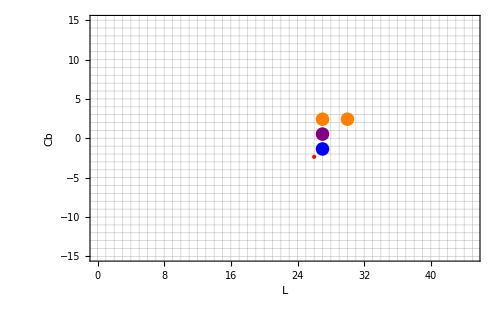
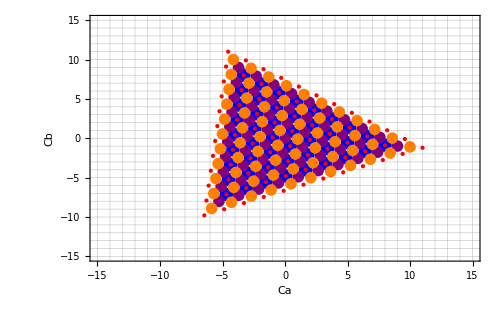
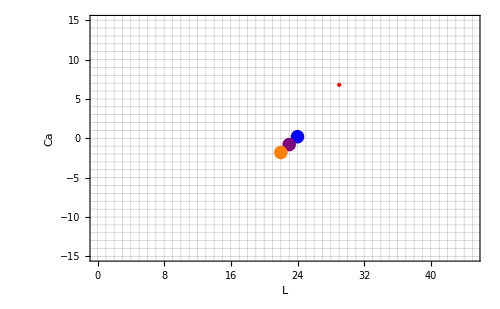

```mathematica
ListPlot3Dto2DSlice[orderedLCaCb16,9,7,7]
```

```mathematica
Manipulate[GraphicsGrid[{
{ListPlot3Dto2DSlice[orderedLCaCb16,9,7,7],MatrixPlot[bins[[All,Ca,All]]]},
{MatrixPlot[bins[[All,All,Cb]]],MatrixPlot[bins[[l,All,All]]]}}],{{l,1},1,Dimensions[bins][[1]],1},{{Ca,1},1,Dimensions[bins][[2]],1},{{Cb,1},1,Dimensions[bins][[3]],1}]
```

```mathematica
Clear[S,T,LCaCb16,orderedLCaCb16,range,indx,shift,dim,bins,pnts]
Block[{θ=N[Pi/11],n=15},
S = {1/3,1,1};
T= fRs[θ];
LCaCb16 = Table[S(T.{r,g,b}),{r,0,n},{g,0,n},{b,0,n}];
orderedLCaCb16=Sort[Flatten[LCaCb16,2]];
Print["Dimensions[LCaCb16] = ",Dimensions[LCaCb16]];
Print["Dimensions[orderedLCaCb16] = ",Dimensions[orderedLCaCb16]];
range={{Min[LCaCb16[[All,All,All,1]]],Max[LCaCb16[[All,All,All,1]]]},{Min[LCaCb16[[All,All,All,2]]],Max[LCaCb16[[All,All,All,2]]]},{Min[LCaCb16[[All,All,All,3]]],Max[LCaCb16[[All,All,All,3]]]}};
Print["Range = ",MatrixForm[range]];
indx=Flatten[Table[Floor[LCaCb16[[r,g,b,All]]],{r,1,n+1},{g,1,n+1},{b,1,n+1}],2];
shift={1-Min[indx[[All,1]]],1-Min[indx[[All,2]]],1-Min[indx[[All,3]]]};
dim={Ceiling@Max[LCaCb16[[All,All,All,1]]]+shift[[1]],Ceiling@Max[LCaCb16[[All,All,All,2]]]+shift[[2]],Ceiling@Max[LCaCb16[[All,All,All,3]]]+shift[[3]]};
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Do[Part[bins,indx[[i,1]]+shift[[1]],indx[[i,2]]+shift[[2]],indx[[i,3]]+shift[[3]]]++,{i,1,Length[indx]}];

]
```

Dimensions[LCaCb16] = {16,16,16,3}

Dimensions[orderedLCaCb16] = {4096,3}

Range = (0. | 15.
-15. | 15.
-15. | 15.)

```mathematica
Block[{pnts=LCaCb16,n=16},
indx=Flatten[Table[Floor[pnts[[r,g,b,All]]],{r,1,n},{g,1,n},{b,1,n}],2];
shift={1-Min[indx[[All,1]]],1-Min[indx[[All,2]]],1-Min[indx[[All,3]]]};
dim={Ceiling@Max[pnts[[All,All,All,1]]]+shift[[1]],Ceiling@Max[pnts[[All,All,All,2]]]+shift[[2]],Ceiling@Max[pnts[[All,All,All,3]]]+shift[[3]]};
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Do[Part[bins,indx[[i,1]]+shift[[1]],indx[[i,2]]+shift[[2]],indx[[i,3]]+shift[[3]]]++,{i,1,Length[indx]}];
]
```

```mathematica
dim
```

{24,31,17}

```mathematica
shift
```

{1,16,9}

```mathematica
GraphicsCubeOpts
```

Sequence[Lighting→Neutral,Axes→True,ViewVertical→{1,0,0},AxesLabel→{Luminosity,Chrom a,Chrom b}]

```mathematica
Dimensions[bins]
```

{25,32,32}

```mathematica
Max[bins]
```

1

```mathematica
Graphics3D[{Raster3D[bins/Max[bins],ColorFunction->"GrayLevelOpacity"]},GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Min[indx[[All,1]]]
```

-7

```mathematica
{Max[indx[[All,1]]],Max[indx[[All,2]]],Max[indx[[All,3]]]}
```

$Aborted[]

```mathematica
T
```

{{1,1,1},{-1/2,1,-1/2},{-1,0,1}}

```mathematica
S
```

{1/2,1,1/2}

```mathematica
analYab16=AnalysePoints[N[orderedYab16]];
analYab16["diffs"]
Block[{vars=(1/analYab16["diffs"]^2)},{Sqrt[1/Round[vars[[1]]]],Sqrt[1/Round[vars[[2]]]],Sqrt[1/Round[vars[[3]]]]}]
```

{0.57735,0.408248,0.707107}

{1/(√3),1/(√6),1/(√2)}

```mathematica
analLCaCb16=AnalysePoints[N[orderedLCaCb16]];
analLCaCb16["diffs"]
analLCaCb16["vals"]
Block[{vars=(1/analLCaCb16["diffs"]^2)},{Sqrt[1/Round[vars[[1]]]],Sqrt[1/Round[vars[[2]]]],Sqrt[1/Round[vars[[3]]]]}]
```

{1.,0.0198789,0.0228296,0.0427085,0.0655381,0.108247,0.173785,0.239323,0.413108,0.0143864,0.0663535,0.0807399,0.0951263,0.109513}

{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.},{-15.,-14.5869,-14.4131,-14.1738,-14.,-13.8262,-13.7607,-13.5869,-13.4131,-13.3476,-13.2393,-13.1738,-13.,-12.9345,-12.8262,-12.7607,-12.6524,-12.5869,-12.5214,-12.4131,-12.3476,-12.2393,-12.1738,-12.1082,-12.0655,-12.,-11.9345,-11.8262,-11.7607,-11.6951,-11.6524,-11.5869,-11.5214,-11.4786,-11.4131,-11.3476,-11.282,-11.2393,-11.1738,-11.1082,-11.0655,-11.,-10.9345,-10.8918,-10.8689,-10.8262,-10.7607,-10.6951,-10.6524,-10.5869,-10.5214,-10.4786,-10.4558,-10.4131,-10.3476,-10.3049,-10.282,-10.2393,-10.1738,-10.1082,-10.0655,-10.0427,-10.,-9.93446,-9.89175,-9.86892,-9.82622,-9.76068,-9.71797,-9.69514,-9.65243,-9.6296,-9.58689,-9.52135,-9.47865,-9.45582,-9.41311,-9.34757,-9.30486,-9.28203,-9.23932,-9.21649,-9.17378,-9.13108,-9.10825,-9.06554,-9.04271,-9.,-8.93446,-8.89175,-8.86892,-8.82622,-8.80339,-8.76068,-8.71797,-8.69514,-8.65243,-8.6296,-8.58689,-8.54418,-8.52135,-8.47865,-8.45582,-8.41311,-8.34757,-8.30486,-8.28203,-8.23932,-8.21649,-8.17378,-8.13108,-8.10825,-8.06554,-8.04271,-8.,-7.95729,-7.93446,-7.89175,-7.86892,-7.82622,-7.80339,-7.76068,-7.71797,-7.69514,-7.65243,-7.6296,-7.58689,-7.54418,-7.52135,-7.47865,-7.45582,-7.41311,-7.3704,-7.34757,-7.30486,-7.28203,-7.23932,-7.21649,-7.17378,-7.13108,-7.10825,-7.06554,-7.04271,-7.,-6.95729,-6.93446,-6.89175,-6.86892,-6.82622,-6.80339,-6.78351,-6.76068,-6.71797,-6.69514,-6.65243,-6.6296,-6.58689,-6.54418,-6.52135,-6.47865,-6.45582,-6.41311,-6.3704,-6.34757,-6.30486,-6.28203,-6.23932,-6.21649,-6.19661,-6.17378,-6.13108,-6.10825,-6.06554,-6.04271,-6.,-5.95729,-5.93446,-5.89175,-5.86892,-5.82622,-5.80339,-5.78351,-5.76068,-5.71797,-5.69514,-5.65243,-5.6296,-5.58689,-5.54418,-5.52135,-5.47865,-5.45582,-5.41311,-5.3704,-5.34757,-5.30486,-5.28203,-5.23932,-5.21649,-5.19661,-5.17378,-5.13108,-5.10825,-5.06554,-5.04271,-5.,-4.95729,-4.93446,-4.89175,-4.86892,-4.82622,-4.80339,-4.78351,-4.76068,-4.71797,-4.69514,-4.65243,-4.6296,-4.58689,-4.54418,-4.52135,-4.47865,-4.45582,-4.41311,-4.3704,-4.34757,-4.30486,-4.28203,-4.23932,-4.21649,-4.19661,-4.17378,-4.13108,-4.10825,-4.06554,-4.04271,-4.,-3.95729,-3.93446,-3.89175,-3.86892,-3.82622,-3.80339,-3.78351,-3.76068,-3.71797,-3.69514,-3.65243,-3.6296,-3.58689,-3.54418,-3.52135,-3.47865,-3.45582,-3.41311,-3.3704,-3.34757,-3.30486,-3.28203,-3.23932,-3.21649,-3.19661,-3.17378,-3.13108,-3.10825,-3.06554,-3.04271,-3.,-2.95729,-2.93446,-2.89175,-2.86892,-2.82622,-2.80339,-2.78351,-2.76068,-2.71797,-2.69514,-2.65243,-2.6296,-2.58689,-2.54418,-2.52135,-2.47865,-2.45582,-2.41311,-2.3704,-2.34757,-2.30486,-2.28203,-2.23932,-2.21649,-2.19661,-2.17378,-2.13108,-2.10825,-2.06554,-2.04271,-2.,-1.95729,-1.93446,-1.89175,-1.86892,-1.82622,-1.80339,-1.78351,-1.76068,-1.71797,-1.69514,-1.65243,-1.6296,-1.58689,-1.54418,-1.52135,-1.47865,-1.45582,-1.41311,-1.3704,-1.34757,-1.30486,-1.28203,-1.23932,-1.21649,-1.19661,-1.17378,-1.13108,-1.10825,-1.06554,-1.04271,-1.,-0.957292,-0.934462,-0.891753,-0.868924,-0.826215,-0.803386,-0.783507,-0.760677,-0.717969,-0.695139,-0.652431,-0.629601,-0.586892,-0.544184,-0.521354,-0.478646,-0.455816,-0.413108,-0.370399,-0.347569,-0.304861,-0.282031,-0.239323,-0.216493,-0.196614,-0.173785,-0.131076,-0.108247,-0.0655381,-0.0427085,-8.88178×10^-16,0.0427085,0.0655381,0.108247,0.131076,0.173785,0.196614,0.216493,0.239323,0.282031,0.304861,0.347569,0.370399,0.413108,0.455816,0.478646,0.521354,0.544184,0.586892,0.629601,0.652431,0.695139,0.717969,0.760677,0.783507,0.803386,0.826215,0.868924,0.891753,0.934462,0.957292,1.,1.04271,1.06554,1.10825,1.13108,1.17378,1.19661,1.21649,1.23932,1.28203,1.30486,1.34757,1.3704,1.41311,1.45582,1.47865,1.52135,1.54418,1.58689,1.6296,1.65243,1.69514,1.71797,1.76068,1.78351,1.80339,1.82622,1.86892,1.89175,1.93446,1.95729,2.,2.04271,2.06554,2.10825,2.13108,2.17378,2.19661,2.21649,2.23932,2.28203,2.30486,2.34757,2.3704,2.41311,2.45582,2.47865,2.52135,2.54418,2.58689,2.6296,2.65243,2.69514,2.71797,2.76068,2.78351,2.80339,2.82622,2.86892,2.89175,2.93446,2.95729,3.,3.04271,3.06554,3.10825,3.13108,3.17378,3.19661,3.21649,3.23932,3.28203,3.30486,3.34757,3.3704,3.41311,3.45582,3.47865,3.52135,3.54418,3.58689,3.6296,3.65243,3.69514,3.71797,3.76068,3.78351,3.80339,3.82622,3.86892,3.89175,3.93446,3.95729,4.,4.04271,4.06554,4.10825,4.13108,4.17378,4.19661,4.21649,4.23932,4.28203,4.30486,4.34757,4.3704,4.41311,4.45582,4.47865,4.52135,4.54418,4.58689,4.6296,4.65243,4.69514,4.71797,4.76068,4.78351,4.80339,4.82622,4.86892,4.89175,4.93446,4.95729,5.,5.04271,5.06554,5.10825,5.13108,5.17378,5.19661,5.21649,5.23932,5.28203,5.30486,5.34757,5.3704,5.41311,5.45582,5.47865,5.52135,5.54418,5.58689,5.6296,5.65243,5.69514,5.71797,5.76068,5.78351,5.80339,5.82622,5.86892,5.89175,5.93446,5.95729,6.,6.04271,6.06554,6.10825,6.13108,6.17378,6.19661,6.21649,6.23932,6.28203,6.30486,6.34757,6.3704,6.41311,6.45582,6.47865,6.52135,6.54418,6.58689,6.6296,6.65243,6.69514,6.71797,6.76068,6.78351,6.80339,6.82622,6.86892,6.89175,6.93446,6.95729,7.,7.04271,7.06554,7.10825,7.13108,7.17378,7.21649,7.23932,7.28203,7.30486,7.34757,7.3704,7.41311,7.45582,7.47865,7.52135,7.54418,7.58689,7.6296,7.65243,7.69514,7.71797,7.76068,7.80339,7.82622,7.86892,7.89175,7.93446,7.95729,8.,8.04271,8.06554,8.10825,8.13108,8.17378,8.21649,8.23932,8.28203,8.30486,8.34757,8.41311,8.45582,8.47865,8.52135,8.54418,8.58689,8.6296,8.65243,8.69514,8.71797,8.76068,8.80339,8.82622,8.86892,8.89175,8.93446,9.,9.04271,9.06554,9.10825,9.13108,9.17378,9.21649,9.23932,9.28203,9.30486,9.34757,9.41311,9.45582,9.47865,9.52135,9.58689,9.6296,9.65243,9.69514,9.71797,9.76068,9.82622,9.86892,9.89175,9.93446,10.,10.0427,10.0655,10.1082,10.1738,10.2393,10.282,10.3049,10.3476,10.4131,10.4558,10.4786,10.5214,10.5869,10.6524,10.6951,10.7607,10.8262,10.8689,10.8918,10.9345,11.,11.0655,11.1082,11.1738,11.2393,11.282,11.3476,11.4131,11.4786,11.5214,11.5869,11.6524,11.6951,11.7607,11.8262,11.9345,12.,12.0655,12.1082,12.1738,12.2393,12.3476,12.4131,12.5214,12.5869,12.6524,12.7607,12.8262,12.9345,13.,13.1738,13.2393,13.3476,13.4131,13.5869,13.7607,13.8262,14.,14.1738,14.4131,14.5869,15.},{-15.,-14.8905,-14.781,-14.6715,-14.5619,-14.4524,-14.3429,-14.2334,-14.1239,-14.1095,-14.0144,-14.,-13.9049,-13.8905,-13.7954,-13.781,-13.6858,-13.6715,-13.5763,-13.5619,-13.4668,-13.4524,-13.3573,-13.3429,-13.2334,-13.219,-13.1239,-13.1095,-13.0144,-13.,-12.9049,-12.8905,-12.7954,-12.781,-12.6858,-12.6715,-12.5763,-12.5619,-12.4668,-12.4524,-12.3573,-12.3429,-12.3285,-12.2334,-12.219,-12.1239,-12.1095,-12.0144,-12.,-11.9049,-11.8905,-11.7954,-11.781,-11.6858,-11.6715,-11.5763,-11.5619,-11.4668,-11.4524,-11.4381,-11.3573,-11.3429,-11.3285,-11.2334,-11.219,-11.1239,-11.1095,-11.0144,-11.,-10.9049,-10.8905,-10.7954,-10.781,-10.6858,-10.6715,-10.5763,-10.5619,-10.5476,-10.4668,-10.4524,-10.4381,-10.3573,-10.3429,-10.3285,-10.2334,-10.219,-10.1239,-10.1095,-10.0144,-10.,-9.90487,-9.89049,-9.79536,-9.78097,-9.68585,-9.67146,-9.65708,-9.57634,-9.56195,-9.54756,-9.46682,-9.45244,-9.43805,-9.35731,-9.34292,-9.32854,-9.23341,-9.21903,-9.1239,-9.10951,-9.01439,-9.,-8.90487,-8.89049,-8.79536,-8.78097,-8.76659,-8.68585,-8.67146,-8.65708,-8.57634,-8.56195,-8.54756,-8.46682,-8.45244,-8.43805,-8.35731,-8.34292,-8.32854,-8.23341,-8.21903,-8.1239,-8.10951,-8.01439,-8.,-7.90487,-7.89049,-7.8761,-7.79536,-7.78097,-7.76659,-7.68585,-7.67146,-7.65708,-7.57634,-7.56195,-7.54756,-7.46682,-7.45244,-7.43805,-7.35731,-7.34292,-7.32854,-7.23341,-7.21903,-7.1239,-7.10951,-7.01439,-7.,-6.98561,-6.90487,-6.89049,-6.8761,-6.79536,-6.78097,-6.76659,-6.68585,-6.67146,-6.65708,-6.57634,-6.56195,-6.54756,-6.46682,-6.45244,-6.43805,-6.35731,-6.34292,-6.32854,-6.23341,-6.21903,-6.1239,-6.10951,-6.09513,-6.01439,-6.,-5.98561,-5.90487,-5.89049,-5.8761,-5.79536,-5.78097,-5.76659,-5.68585,-5.67146,-5.65708,-5.57634,-5.56195,-5.54756,-5.46682,-5.45244,-5.43805,-5.35731,-5.34292,-5.32854,-5.23341,-5.21903,-5.20464,-5.1239,-5.10951,-5.09513,-5.01439,-5.,-4.98561,-4.90487,-4.89049,-4.8761,-4.79536,-4.78097,-4.76659,-4.68585,-4.67146,-4.65708,-4.57634,-4.56195,-4.54756,-4.46682,-4.45244,-4.43805,-4.35731,-4.34292,-4.32854,-4.31415,-4.23341,-4.21903,-4.20464,-4.1239,-4.10951,-4.09513,-4.01439,-4.,-3.98561,-3.90487,-3.89049,-3.8761,-3.79536,-3.78097,-3.76659,-3.68585,-3.67146,-3.65708,-3.57634,-3.56195,-3.54756,-3.46682,-3.45244,-3.43805,-3.42366,-3.35731,-3.34292,-3.32854,-3.31415,-3.23341,-3.21903,-3.20464,-3.1239,-3.10951,-3.09513,-3.01439,-3.,-2.98561,-2.90487,-2.89049,-2.8761,-2.79536,-2.78097,-2.76659,-2.68585,-2.67146,-2.65708,-2.57634,-2.56195,-2.54756,-2.53318,-2.46682,-2.45244,-2.43805,-2.42366,-2.35731,-2.34292,-2.32854,-2.31415,-2.23341,-2.21903,-2.20464,-2.1239,-2.10951,-2.09513,-2.01439,-2.,-1.98561,-1.90487,-1.89049,-1.8761,-1.79536,-1.78097,-1.76659,-1.68585,-1.67146,-1.65708,-1.64269,-1.57634,-1.56195,-1.54756,-1.53318,-1.46682,-1.45244,-1.43805,-1.42366,-1.35731,-1.34292,-1.32854,-1.31415,-1.23341,-1.21903,-1.20464,-1.1239,-1.10951,-1.09513,-1.01439,-1.,-0.985614,-0.904874,-0.890487,-0.876101,-0.795361,-0.780975,-0.766588,-0.685848,-0.671462,-0.657076,-0.642689,-0.576336,-0.561949,-0.547563,-0.533177,-0.466823,-0.452437,-0.438051,-0.423664,-0.357311,-0.342924,-0.328538,-0.314152,-0.233412,-0.219025,-0.204639,-0.123899,-0.109513,-0.0951263,-0.0143864,0.,0.0143864,0.0951263,0.109513,0.123899,0.204639,0.219025,0.233412,0.314152,0.328538,0.342924,0.357311,0.423664,0.438051,0.452437,0.466823,0.533177,0.547563,0.561949,0.576336,0.642689,0.657076,0.671462,0.685848,0.766588,0.780975,0.795361,0.876101,0.890487,0.904874,0.985614,1.,1.01439,1.09513,1.10951,1.1239,1.20464,1.21903,1.23341,1.31415,1.32854,1.34292,1.35731,1.42366,1.43805,1.45244,1.46682,1.53318,1.54756,1.56195,1.57634,1.64269,1.65708,1.67146,1.68585,1.76659,1.78097,1.79536,1.8761,1.89049,1.90487,1.98561,2.,2.01439,2.09513,2.10951,2.1239,2.20464,2.21903,2.23341,2.31415,2.32854,2.34292,2.35731,2.42366,2.43805,2.45244,2.46682,2.53318,2.54756,2.56195,2.57634,2.65708,2.67146,2.68585,2.76659,2.78097,2.79536,2.8761,2.89049,2.90487,2.98561,3.,3.01439,3.09513,3.10951,3.1239,3.20464,3.21903,3.23341,3.31415,3.32854,3.34292,3.35731,3.42366,3.43805,3.45244,3.46682,3.54756,3.56195,3.57634,3.65708,3.67146,3.68585,3.76659,3.78097,3.79536,3.8761,3.89049,3.90487,3.98561,4.,4.01439,4.09513,4.10951,4.1239,4.20464,4.21903,4.23341,4.31415,4.32854,4.34292,4.35731,4.43805,4.45244,4.46682,4.54756,4.56195,4.57634,4.65708,4.67146,4.68585,4.76659,4.78097,4.79536,4.8761,4.89049,4.90487,4.98561,5.,5.01439,5.09513,5.10951,5.1239,5.20464,5.21903,5.23341,5.32854,5.34292,5.35731,5.43805,5.45244,5.46682,5.54756,5.56195,5.57634,5.65708,5.67146,5.68585,5.76659,5.78097,5.79536,5.8761,5.89049,5.90487,5.98561,6.,6.01439,6.09513,6.10951,6.1239,6.21903,6.23341,6.32854,6.34292,6.35731,6.43805,6.45244,6.46682,6.54756,6.56195,6.57634,6.65708,6.67146,6.68585,6.76659,6.78097,6.79536,6.8761,6.89049,6.90487,6.98561,7.,7.01439,7.10951,7.1239,7.21903,7.23341,7.32854,7.34292,7.35731,7.43805,7.45244,7.46682,7.54756,7.56195,7.57634,7.65708,7.67146,7.68585,7.76659,7.78097,7.79536,7.8761,7.89049,7.90487,8.,8.01439,8.10951,8.1239,8.21903,8.23341,8.32854,8.34292,8.35731,8.43805,8.45244,8.46682,8.54756,8.56195,8.57634,8.65708,8.67146,8.68585,8.76659,8.78097,8.79536,8.89049,8.90487,9.,9.01439,9.10951,9.1239,9.21903,9.23341,9.32854,9.34292,9.35731,9.43805,9.45244,9.46682,9.54756,9.56195,9.57634,9.65708,9.67146,9.68585,9.78097,9.79536,9.89049,9.90487,10.,10.0144,10.1095,10.1239,10.219,10.2334,10.3285,10.3429,10.3573,10.4381,10.4524,10.4668,10.5476,10.5619,10.5763,10.6715,10.6858,10.781,10.7954,10.8905,10.9049,11.,11.0144,11.1095,11.1239,11.219,11.2334,11.3285,11.3429,11.3573,11.4381,11.4524,11.4668,11.5619,11.5763,11.6715,11.6858,11.781,11.7954,11.8905,11.9049,12.,12.0144,12.1095,12.1239,12.219,12.2334,12.3285,12.3429,12.3573,12.4524,12.4668,12.5619,12.5763,12.6715,12.6858,12.781,12.7954,12.8905,12.9049,13.,13.0144,13.1095,13.1239,13.219,13.2334,13.3429,13.3573,13.4524,13.4668,13.5619,13.5763,13.6715,13.6858,13.781,13.7954,13.8905,13.9049,14.,14.0144,14.1095,14.1239,14.2334,14.3429,14.4524,14.5619,14.6715,14.781,14.8905,15.}}

{1,1/(√2531),1/(√1919)}

```mathematica
T . {1,3,1}
S%
```

{5,2,0}

{5/2,2,0}

```mathematica
Clear[AnalysePoints]
AnalysePoints[pts_]:=Module[{analysed},
analysed["vals"]={Union[N[pts[[All,1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[N[pts[[All,2]]],SameTest->(Abs[#1-#2]≤0.001&)],Union[N[pts[[All,3]]],SameTest->(Abs[#1-#2]≤0.001&)]};
analysed["diffs"]=Flatten[{
Union[Rest[analysed["vals"][[1]]]-Most[analysed["vals"][[1]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[2]]]-Most[analysed["vals"][[2]]],SameTest->(Abs[#1-#2]≤0.001&)],
Union[Rest[analysed["vals"][[3]]]-Most[analysed["vals"][[3]]],SameTest->(Abs[#1-#2]≤0.001&)]}];
 analysed
]
```

```mathematica
orderedLCaCb16=Sort[Flatten[LCaCb16,2]];
```

```mathematica
Dimensions[%1731]
```

{6,7,8,3}

```mathematica
scale["nLCaCb","fR"][0]
```

scale[nLCaCb,fR][0]

```mathematica
scale["LCaCb","fR"] fR[0]
```

{{1,1,1},{-1/2,1,-1/2},{-1,0,1}}

```mathematica
Simplify[1/(2 √(2/3))]
N[1/(√6)]
```

(√(3/2))/2

0.408248

```mathematica
{0.7071067811865461^2,0.4082482904638596^2,0.5773502691896226^2}
```

{0.5,0.166667,0.333333}

```mathematica
scale["LCaCb","nLCaCb"][0]
```

{√3,2 √(2/3),√2}

```mathematica
{Max[CaVals],N[10 √6]}
```

{24.8114,24.4949}

```mathematica
CaDiv=Table[i scale["LCaCb","nLCaCb"][0][[2]],{i,0,15}]
CbDiv=Table[i scale["LCaCb","nLCaCb"][0][[3]],{i,0,15}]
```

{0,2 √(2/3),4 √(2/3),2 √6,8 √(2/3),10 √(2/3),4 √6,14 √(2/3),16 √(2/3),6 √6,20 √(2/3),22 √(2/3),8 √6,26 √(2/3),28 √(2/3),10 √6}

```mathematica
Range[Min[vals[[3]]],Max[vals[[3]]]]
```

```mathematica
Union[N[orderedLCaCb16[[All,1]]]]
```

{0.,0.57735,1.1547,1.73205,2.3094,2.3094,2.88675,3.4641,4.04145,4.6188,4.6188,5.19615,5.7735,6.35085,6.35085,6.9282,7.50555,7.50555,8.0829,8.66025,9.2376,9.2376,9.81495,9.81495,10.3923,10.9697,10.9697,11.547,11.547,12.1244,12.7017,12.7017,12.7017,13.2791,13.2791,13.2791,13.8564,14.4338,14.4338,15.0111,15.0111,15.5885,16.1658,16.1658,16.7432,16.7432,17.3205,17.8979,17.8979,18.4752,18.4752,19.0526,19.6299,19.6299,20.2073,20.2073,20.2073,20.7846,21.362,21.362,21.362,21.9393,21.9393,22.5167,23.094,23.094,23.6714,23.6714,24.2487,24.8261,25.4034,25.9808}

```mathematica
Range[Min[analLCaCb16["vals"][[3]]],Max[analLCaCb16["vals"][[3]]]]
```

{-7.5,-6.5,-5.5,-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5}

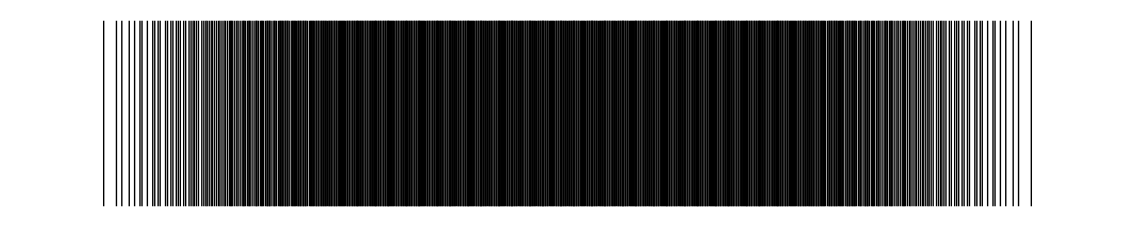

```mathematica
Graphics[Map[Line[{{#1,0},{#1,1}}]&,analLCaCb16["vals"][[2]]]]
```

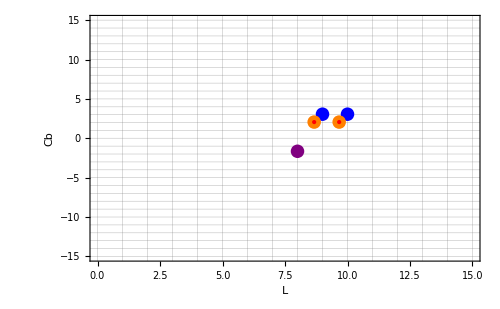
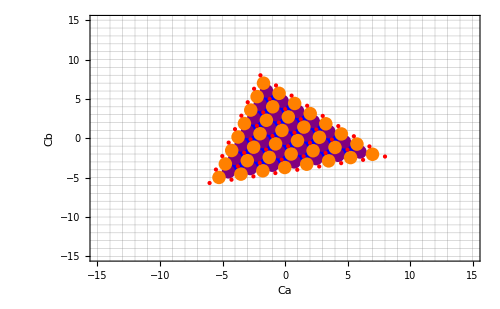
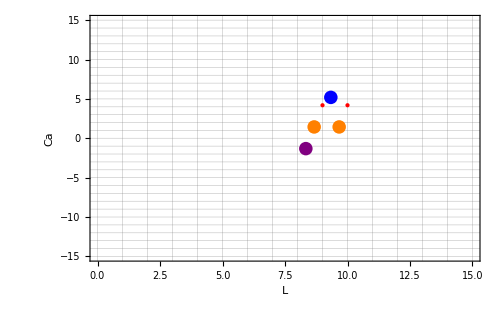

-Graphics3D-

```mathematica
ListPlot3Dto2DSlice[orderedLCaCb16,6,10,10]
ListPointPlot3D[orderedLCaCb16]
```

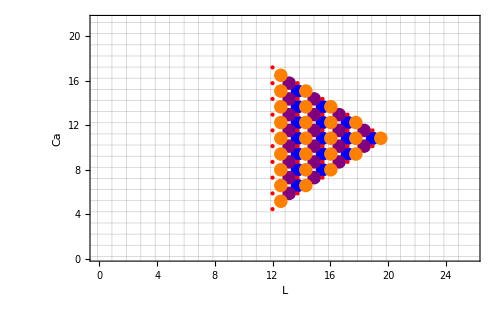
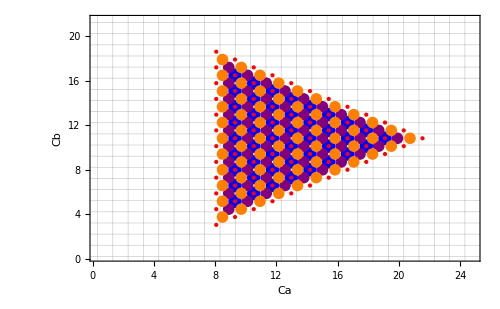
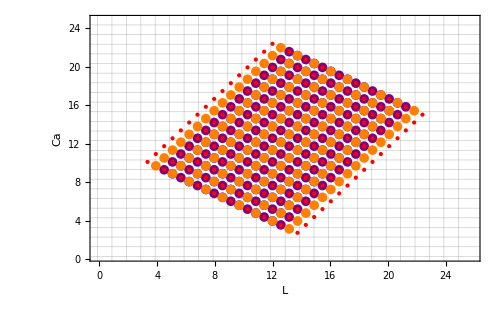

```mathematica
ListPlot3Dto2DSlice[orderedYab16,9,7,7]
```

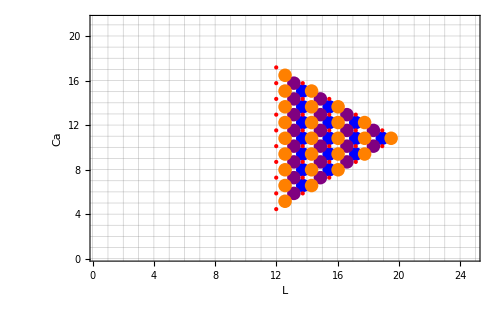
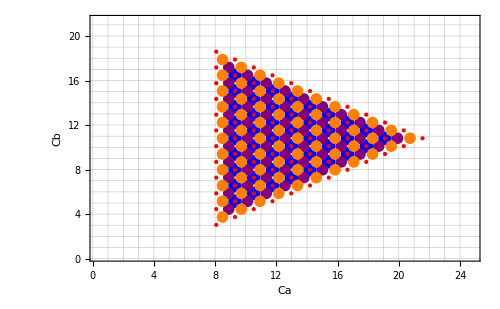
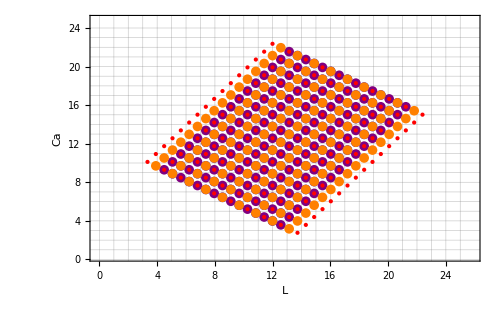

```mathematica
Block[{L=9,Ca=7,Cb=7},Row[{Show[{
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca]],_}]][[All,{1,3}]],PlotStyle->Blue],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+1]],_}]][[All,{1,3}]],PlotStyle->Purple],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+2]],_}]][[All,{1,3}]],PlotStyle->Orange],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+3]],_}]][[All,{1,3}]],PlotStyle->Directive[Red,PointSize[Small]]]},PlotRange->{{Min[CaVals],Max[CaVals]},{Min[CbVals],Max[CbVals]}},Frame->True,FrameLabel->{{"Ca",None},{"L",None}},GridLines->{Range[0,Max[LVals]],Range[0,Max[CbVals]]},ImageSize->500],
Show[{ListPlot[Extract[orderedYab16,Position[orderedYab16,{LVals[[L]],_,_}]][[All,{2,3}]],PlotStyle->Blue,PlotRange->{{Min[CaVals],Max[CaVals]},{Min[CbVals],Max[CbVals]}}],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{LVals[[L+1]],_,_}]][[All,{2,3}]],PlotStyle->Purple],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{LVals[[L+2]],_,_}]][[All,{2,3}]],PlotStyle->Orange],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{LVals[[L+3]],_,_}]][[All,{2,3}]],PlotStyle->Directive[Red,PointSize[Small]]]},PlotRange->{{Min[CaVals],Max[CaVals]},{Min[CbVals],Max[CbVals]}},Frame->True,FrameLabel->{{"Cb",None},{"Ca",None}},GridLines->{Range[0,Max[CaVals]],Range[0,Max[CbVals]]},ImageSize->500],
Show[{
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb]]}]][[All,{1,2}]],PlotStyle->Blue],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+1]]}]][[All,{1,2}]],PlotStyle->Purple],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+2]]}]][[All,{1,2}]],PlotStyle->Orange],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+3]]}]][[All,{1,2}]],PlotStyle->Directive[Red,PointSize[Small]]]},PlotRange->{{Min[LVals],Max[LVals]},{Min[CaVals],Max[CaVals]}},Frame->True,FrameLabel->{{"Ca",None},{"L",None}},GridLines->{Range[0,Max[LVals]],Range[0,Max[CaVals]]},ImageSize->500]
}]
]
```

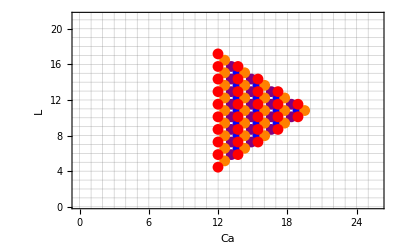

```mathematica
Block[{Ca=7},
Show[{ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca]],_}]][[All,{1,3}]],PlotStyle->Blue],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+1]],_}]][[All,{1,3}]],PlotStyle->Purple],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+2]],_}]][[All,{1,3}]],PlotStyle->Orange],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+3]],_}]][[All,{1,3}]],PlotStyle->Red]},PlotRange->{{Min[LVals],Max[LVals]},{Min[CbVals],Max[CbVals]}},Frame->True,FrameLabel->{{"L",None},{"Ca",None}},GridLines->{Range[0,Max[LVals]],Range[0,Max[CbVals]]}]
]
```

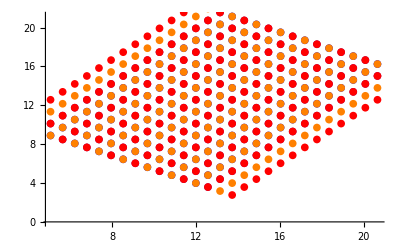

```mathematica
Block[{Cb=7},
Show[{ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb]]}]][[All,{1,2}]],PlotStyle->Blue],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+1]]}]][[All,{1,2}]],PlotStyle->Purple],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+2]]}]][[All,{1,2}]],PlotStyle->Orange],
ListPlot[Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+3]]}]][[All,{1,2}]],PlotStyle->Red]}]
]
```

```mathematica
Block[{L=7,Ca=7,Cb=7},
ListPointPlot3D[Flatten[{Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca]],_}]],Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+1]],_}]],Extract[orderedYab16,Position[orderedYab16,{_,CaVals[[Ca+2]],_}]],
Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb]]}]],
Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+1]]}]],
Extract[orderedYab16,Position[orderedYab16,{_,_,CbVals[[Cb+2]]}]],
Extract[orderedYab16,Position[orderedYab16,{LVals[[L]],_,_}]],
Extract[orderedYab16,Position[orderedYab16,{LVals[[L+1]],_,_}]],
Extract[orderedYab16,Position[orderedYab16,{LVals[[L+2]],_,_}]]},1]]
]
```

-Graphics3D-

```mathematica
N[46/3]
```

15.3333

```mathematica
Dimensions[orderedYab16]
```

{4096,3}

```mathematica
Sort
```

```mathematica
orderedYab16[[1,2,3,All]]
```

{1.59808,13.7887,10.1066}

```mathematica
FlattenAt
```

```mathematica
Dimensions[Transpose[mapYab16,{4,3,2,1}]]
```

{16,16,16,3}

```mathematica
test=Table[0,{l,0,2},{i,0,3},{j,0,4},{k,0,5}];
```

```mathematica
Dimensions[%1121]
```

{3,4,5,6}

```mathematica
Permutations[{4,3,2,1}]
```

{{4,3,2,1},{4,3,1,2},{4,2,3,1},{4,2,1,3},{4,1,3,2},{4,1,2,3},{3,4,2,1},{3,4,1,2},{3,2,4,1},{3,2,1,4},{3,1,4,2},{3,1,2,4},{2,4,3,1},{2,4,1,3},{2,3,4,1},{2,3,1,4},{2,1,4,3},{2,1,3,4},{1,4,3,2},{1,4,2,3},{1,3,4,2},{1,3,2,4},{1,2,4,3},{1,2,3,4}}

```mathematica
Map[Dimensions[Transpose[test,#]]&,Permutations[{4,3,2,1}]]
```

{{6,5,4,3},{5,6,4,3},{6,4,5,3},{5,4,6,3},{4,6,5,3},{4,5,6,3},{6,5,3,4},{5,6,3,4},{6,4,3,5},{5,4,3,6},{4,6,3,5},{4,5,3,6},{6,3,5,4},{5,3,6,4},{6,3,4,5},{5,3,4,6},{4,3,6,5},{4,3,5,6},{3,6,5,4},{3,5,6,4},{3,6,4,5},{3,5,4,6},{3,4,6,5},{3,4,5,6}}

```mathematica
Dimensions[Transpose[test,{4,1,2,3}]]
Dimensions[Transpose[test,{4,3,2,1}]]
```

{4,5,6,3}

{6,5,4,3}

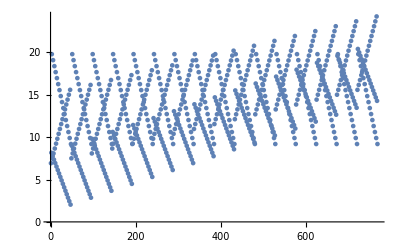

```mathematica
ListPlot[Flatten[Transpose[mapYab16,{4,3,2,1}][[All,All,13,All]]]]
```

```mathematica
Max[bins]
```

2

```mathematica
Manipulate[GraphicsGrid[{{,},{,MatrixPlot[bins[[l,All,All]]]}},{l,1,Dimensions[bins][[1]],1}]
```

```mathematica
GraphicsCube[{Raster3D[speck16Bin/Max[speck16Bin],ColorFunction->"GrayLevelOpacity"]}]
```

-Graphics3D-